```mathematica
DSolve[{y''[x]+y[x]*x^2m^4==0},y[x],x]
```

{{y[x]→C[1] ParabolicCylinderD[-1/2,(-1)^(1/4) √2 m x]+C[2] ParabolicCylinderD[-1/2,(-1)^(3/4) √2 m x]}}

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
ParabolicCylinderD[-1/2,0]
```

(√π)/(2^(1/4) Gamma[3/4])

```mathematica
D[ParabolicCylinderD[-1/2,x],x]
```

1/2 x ParabolicCylinderD[-1/2,x]-ParabolicCylinderD[1/2,x]

```mathematica
Sol[x_,m_]:=ParabolicCylinderD[-1/2,m(1+I)x]-ParabolicCylinder[-1/2,m(-1+I)x]
```

```mathematica
FullSimplify[D[Sol[x],x]/.{x->1}]
```

Sol'[1]

```mathematica
der[m_]:=ⅈ m (m ParabolicCylinderD[-1/2,(1+ⅈ) m]-(1-ⅈ) (ParabolicCylinderD[1/2,(1+ⅈ) m]+ⅈ Derivative[0,1][ParabolicCylinder][-1/2,(-1+ⅈ) m]))
```

```mathematica
NSolve[der[m]==0,m]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{m→0.}}

```mathematica
FindRoot[der[m]==0,{m,0.1}]
```

FindRoot::nlnum: The function value {(0.`  + 0.1` ⅈ) ((0.11581335375890106`  - 0.0058136541018157` ⅈ) - (1.`  - 1.` ⅈ) ((0.6423699994229543`  + 0.054797137183475245` ⅈ) + (0.`  + 1.` ⅈ) SuperscriptBox[ is not a list of numbers with dimensions {1} at {m} = {0.1`}.

FindRoot[der[m]==0,{m,0.1}]

```mathematica
N[FullSimplify[der[0.1]]]
```

(-0.0581759-0.0581354 ⅈ)+(0.1-0.1 ⅈ) ParabolicCylinder^(0,1)[-0.5,-0.1+0.1 ⅈ]

```mathematica
N[Derivative[0,1][ParabolicCylinder][-0.5,0.1]]
```

ParabolicCylinder^(0,1)[-0.5,0.1]

```mathematica
N[BesselJ[-1/4,1]]
```

0.669385

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

```mathematica
fun1[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]+BesselJ[1/4,x^2/4])
```

```mathematica
fun2[x_]:=2^{-5/4}*Sqrt[π x]*(BesselJ[-1/4,x^2/4]-BesselJ[1/4,x^2/4])
```

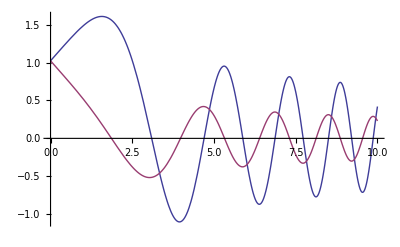

```mathematica
Plot[{fun1[x],fun2[x]},{x,0,10}]
```

```mathematica
funm1[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]+BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funm2[x_]:=1/2 √π √(m x) (BesselJ[-1/4,(m^2 x^2)/2]-BesselJ[1/4,(m^2 x^2)/2])
```

```mathematica
funderm1=FullSimplify[D[funm1[x],x]]
```

1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]-BesselJ[3/4,(m^2 x^2)/2])

```mathematica
funderm2=FullSimplify[D[funm2[x],x]]
```

-1/2 m √π (m x)^(3/2) (BesselJ[-3/4,(m^2 x^2)/2]+BesselJ[3/4,(m^2 x^2)/2])

```mathematica
NSolve[funm1[0]*funderm2[1]-funm2[0]*funderm1[1]==0,m]
```

∞::indet: Indeterminate expression 0 √π ComplexInfinity encountered.

{{}}

```mathematica
Limit[funm1[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[funm2[x],x->0]
```

((m^2)^(3/4) √(π/2))/(m^(3/2) Gamma[3/4])

```mathematica
FullSimplify[funderm1/.{x->1}]
```

1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[funderm2/.{x->1}]
```

-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])

```mathematica
FullSimplify[-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]+BesselJ[3/4,m^2/2])-1/2 m^(5/2) √π (BesselJ[-3/4,m^2/2]-BesselJ[3/4,m^2/2])==0]
```

m^(5/2) BesselJ[-3/4,m^2/2]==0

```mathematica
BesselJZero[-3/4,10]
```

BesselJZero[-3/4,10]

```mathematica
N[BesselJZero[-3/4,1]]
```

1.05851

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,100}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781}

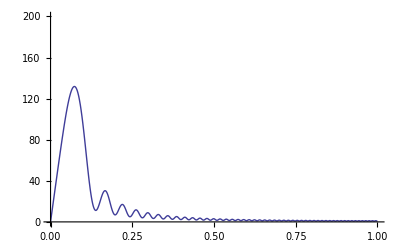

```mathematica
Plot[Sum[(funm1[x]/.{m->Zeros[[i]]})-(funm2[x]/.{m->Zeros[[i]]}),{i,1,100}],{x,0,1},PlotRange->{{0,1},{0,200}}]
```

## Testing solution

```mathematica
test=Sqrt[π x]*BesselJ[-1/4,x^2/4]
```

√π √x BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]]
```

-1/4 √π x^(5/2) BesselJ[-1/4,x^2/4]

```mathematica
FullSimplify[D[test,{x,2}]+x^2/4*test]
```

0

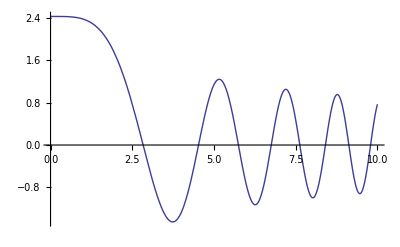

```mathematica
Plot[test,{x,0,10}]
```

```mathematica
sol1=Sqrt[m x]*BesselJ[-1/4,m^2 x^2/2]
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
sol1
```

√x BesselJ[-1/3,2/3 m x^(3/2)]

```mathematica
sol2=Sqrt[m x]*BesselJ[1/4,m^2 x^2/2]
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Limit[sol1,x->0]
```

(√2 (m^2)^(3/4))/(m^(3/2) Gamma[3/4])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
sol1
```

√(m x) BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m (m x)^(3/2) BesselJ[3/4,(m^2 x^2)/2]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m (m x)^(3/2) BesselJ[-3/4,(m^2 x^2)/2]

```mathematica
Limit[dersol1,x->1]
```

-m^(5/2) BesselJ[3/4,m^2/2]

```mathematica
Limit[dersol2,x->1]
```

m^(5/2) BesselJ[-3/4,m^2/2]

```mathematica
Zerostrue=Table[Sqrt[2BesselJZero[-3/4,i]],{i,1,80}];
```

```mathematica
coeffs=Table[BesselJZero[-3/4,i],{i,1,200}];
```

```mathematica
Zeros=Table[N[Sqrt[2BesselJZero[-3/4,i]],10],{i,1,160}]
```

{1.454997085,2.927133004,3.857578101,4.601777732,5.240824067,5.809787864,6.327694301,6.806248002,7.25326169,7.6742593,8.073317953,8.453548974,8.817390869,9.166797024,9.503360989,9.828402986,10.14303138,10.44818742,10.74467855,11.0332036,11.31437223,11.58872006,11.8567207,12.11879537,12.37532065,12.62663484,12.8730432,13.11482231,13.3522237,13.58547689,13.81479204,14.04036213,14.26236488,14.48096438,14.69631251,14.90855018,15.11780841,15.32420926,15.5278667,15.72888729,15.92737088,16.12341118,16.31709625,16.508509,16.69772758,16.88482577,17.06987328,17.25293611,17.43407678,17.61335459,17.79082587,17.96654416,18.14056039,18.31292309,18.48367852,18.65287083,18.82054216,18.98673282,19.15148136,19.31482468,19.47679813,19.63743561,19.79676966,19.95483148,20.11165108,20.26725729,20.42167785,20.57493946,20.72706782,20.87808772,21.02802303,21.17689679,21.32473123,21.47154783,21.61736732,21.76220974,21.90609448,22.04904029,22.1910653,22.3321871,22.47242269,22.61178856,22.7503007,22.88797461,23.02482533,23.16086744,23.29611511,23.4305821,23.56428178,23.69722713,23.82943078,23.96090501,24.09166175,24.22171263,24.35106896,24.47974174,24.60774171,24.7350793,24.86176469,24.98780781,25.11321832,25.23800565,25.36217901,25.48574737,25.60871948,25.7311039,25.85290896,25.97414283,26.09481347,26.21492864,26.33449595,26.45352284,26.57201655,26.6899842,26.80743273,26.92436894,27.04079946,27.1567308,27.27216934,27.38712129,27.50159277,27.61558975,27.72911807,27.84218348,27.95479159,28.0669479,28.17865781,28.28992661,28.40075948,28.5111615,28.62113767,28.73069287,28.83983189,28.94855946,29.05688017,29.16479858,29.27231912,29.37944617,29.48618402,29.59253687,29.69850887,29.80410407,29.90932646,30.01417998,30.11866846,30.2227957,30.32656541,30.42998126,30.53304684,30.63576569,30.73814128,30.84017702,30.94187629,31.04324239,31.14427857,31.24498803,31.34537392,31.44543935,31.54518735,31.64462094}

```mathematica
1.45499708549819386722507026854180579346`10.,2.92713300440027766553121136094888110735`10.,3.8575781013492938200342434118812546441`10.,4.60177773228129985324241798621793597148`10.,5.24082406699070314354952418816449605517`10.,5.80978786426398906487468774457944491812`10.,6.32769430108396681532057061373337375445`10.,6.8062480022514212669586769504065468988`10.,7.25326168965686308822824791463505009483`10.,7.6742592995607184149250788121278225534`10.,8.07331795319108946335626947213305371378`10.,8.45354897437340233163926840148873400306`10.,8.81739086884080680472896916336389339722`10.,9.16679702363228751221979864959553140746`10.,9.50336098897760887069148869968298949199`10.,9.82840298647447126437751319761265707777`10.,10.14303137712219911244514916412671544951`10.,10.44818741811621983414432659838862125807`10.,10.74467854808127573053205335964669225223`10.,11.03320360258297538892991564331548075855`10.,11.31437222998145142057443770168774860219`10.,11.58872005940677119103217820431909528765`10.,11.85672070452047449321754322768063874146`10.,12.11879537438111167446084673341581712359`10.,12.37532064988645588833414500384166974648`10.,12.62663483645073127192279608364483685065`10.,12.8730431991488418101183117224826294002`10.,13.11482231162738863620077232279337810946`10.,13.35222369554359348133575969794532279845`10.,13.58547688707664934803393403887138075079`10.,13.81479203704230978691485194517723996389`10.,14.0403621284925403691860805796792028747`10.,14.2623648784142054972133104428159388272`10.,14.4809643768493324602515059590286238574`10.,14.69631250643745383397730190280670992963`10.,14.90855017729768053412230968849290743382`10.,15.11780840578937570988470787292523813834`10.,15.32420926061949995243758582398480085884`10.,15.52786669570596600871656820859722187773`10.,15.7288872859366536654040406731452138516`10.,15.9273708793136173631920062299682027691`10.,16.12341117681167755300451799359118160072`10.,16.31709624950989469369530608919286116217`10.,16.50850900109559236347854935232210542604`10.,16.69772758263279807557262678658274113287`10.,16.88482576548234240189867071924417329888`10.,17.0698732774215122579902242575503858456`10.,17.25293610630693319483410269200861091738`10.,17.43407677503112073131534139072114313752`10.,17.61335459102147480760264415427211297139`10.,17.79082587310469749719229172428528076748`10.,17.96654415819694343585843588062836815013`10.,18.14056038997006420349764940438806368648`10.,18.31292309137856038366383535925968134061`10.,18.48367852270329730273712784271426510892`10.,18.65287082657088177261838964015053009292`10.,18.82054216123703645850384614058496825444`10.,18.98673282327435071906554950975388778683`10.,19.15148136067609592105538219021147335869`10.,19.31482467727557424266429445652771548091`10.,19.47679812928237338488715497506428607718`10.,19.63743561465094432179652946866365109956`10.,19.79676965592142972660408702565954850112`10.,19.95483147710622580687699207508067817164`10.,20.1116510751371510811081913728251719114`10.,20.26725728633629104179428517626838796877`10.,20.42167784832770592539536914201674076594`10.,20.5749394577664739838553947225769077593`10.,20.72706782422534501022699390743200749406`10.,20.87808772054703867991961754439254908311`10.,21.02802302994145620306095998066847616749`10.,21.17689679008136355778581681928277317273`10.,21.32473123442708740654118303228698174865`10.,21.47154783099012537957908642158269803669`10.,21.61736731872703613437482639643069462277`10.,21.76220974173830183110201170131191655663`10.,21.90609448143183688097899306297480577485`10.,22.0490402867972684906486490578908342351`10.,22.19106530292487557569193393086240056928`10.,22.33218709789200145155224658654248859863`10.,22.47242268812972763181726728233480068426`10.,22.61178856237350107116482179887720435212`10.,22.75030070429314808911143247007435463568`10.,22.88797461389019898535743216669742834062`10.,23.02482532774361176686908350481669578922`10.,23.16086743817875377107897094013951992889`10.,23.29611511142881612007056991591400670695`10.,23.43058210485264430911534250581744912669`10.,23.56428178326822106049067042363678474115`10.,23.69722713445669222196499462428128809258`10.,23.82943078388784484123560074037466926473`10.,23.96090500871429448226506215187209941985`10.,24.09166175107828578483607659944185750049`10.,24.22171263077192876006624179524327743237`10.,24.35106895728885870286413371602770640852`10.,24.47974174130269770440759596094085980563`10.,24.60774170560529058502534730748486421888`10.,24.73507929553546962640942278460409394305`10.,24.86176468892705450126529037039701151511`10.,24.98780780560290158433514050182926229463`10.,25.11321831644006708870055811559405011212`10.,25.23800565202952916807855725233848557165`10.,25.36217901095241434764955105803052194794`10.,25.48574736769328349128365881159583403571`10.,25.60871948020974298826286481975975821267`10.,25.73110389717644977090884369535145447412`10.,25.85290896492046671466441961895419977548`10.,25.97414283406389114600188817002274285412`10.,26.09481346588871741131460938622563226671`10.,26.21492863843799910251461835808144532308`10.,26.33449595236654244200346861227048588322`10.,26.45352283655358479297050162584261891475`10.,26.57201655348918697331695241490058544311`10.,26.68998420444539106900228677122542365513`10.,26.80743273444256315115350431279997534856`10.,26.92436893702074938634192144279007313002`10.,27.04079945882532144885899301531481996968`10.,27.15673080401567010330138314407973778928`10.,27.27216933850522175671071533349314030512`10.,27.38712129404059931904444842046619226734`10.,27.5015927721273236836935924258084318931`10.,27.61558974780905354225731176234972335349`10.,27.7291180733069872325213158703418891891`10.,27.84218348152569918138829195005926719402`10.,27.95479158943135367217217459578099206443`10.,28.06694790130792868493048549539313948149`10.,28.17865781189679108601986330122701795418`10.,28.28992660942469023626614819841869888214`10.,28.40075947852497899599227553112094158799`10.,28.51116150305662806454610751360670020052`10.,28.62113766882537061488637648812395120886`10.,28.73069286621109835498093694749057922709`10.,28.83983189270542661807516764707431009937`10.,28.94855945536315406496103915669137916186`10.,29.0568801731711613409334377673415823046`10.,29.16479857933812188755478470256750080465`10.,29.27231912350823643173581130305598484097`10.,29.37944617390204987306787317871788072344`10.,29.48618401938726481655462124120669710125`10.,29.59253687148232934120849531844604066321`10.,29.69850886629544727947065323370919097601`10.,29.80410406640153686430690657788455184085`10.,29.90932646265954766612311748559774855157`10.,30.01417997597243590390627603971350150613`10.,30.11866845899199411336949914690532327191`10.,30.22279569777063245220418800300579966128`10.,30.32656541336211530366113731323828860625`10.,30.42998126337316800985656774510794595015`10.,30.53304684346778424965974281784788344284`10.,30.63576568882598451462550996210811760772`10.,30.73814127555870008843862044749237208531`10.,30.84017702208038467423650413525089107265`10.,30.94187629044088712766532761964247197981`10.,31.04324238761805344250874245193788967589`10.,31.14427856677246401343051602820994092765`10.,31.24498802846565309148851505340619403559`10.,31.34537392184310108800767554807196747595`10.,31.44543934578323681652762544616436194505`10.,31.54518735001363574556992207115040025218`10.,31.64462093619555173030629520550814059172`10.
```

```mathematica
Table[N[BesselJZero[-3/4,i],10],{i,1,10}]
```

{1.058508259,4.284053813,7.440454404,10.58817915,13.73311845,16.87681751,20.01985758,23.16250593,26.30490257,29.4471279}

```mathematica
N[BesselJ[3/4,BesselJZero[-3/4,3]]]
```

0.207121

```mathematica
N[BesselJ[1/4,BesselJZero[-3/4,1]]]
```

0.742897

```mathematica
sol2
```

√(m x) BesselJ[1/4,(m^2 x^2)/2]

```mathematica
sol2m=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
Plot[Sum[(sol2m/.{m->Zerostrue[[i]]}),{i,1,10}],{x,0,1},PlotRange->{{0,1},{0,100}}]
```

$Aborted

```mathematica
NIntegrate[x^3 BesselJ[1/4,x^2/2*Zerostrue[[2]]^2]*BesselJ[1/4,x^2/2*Zerostrue[[2]]^2],{x,0,1}]
```

0.0368546

```mathematica
wmcubic=Table[NIntegrate[x^3 BesselJ[1/4,x^2/2*Zeros[[i]]^2]^2,{x,0,1}],{i,81,160}]
```

NIntegrate::precw: The precision of the argument function (x^3 BesselJ[1/4, 252.50489073698386684851928257492913473823`9.698970004336022 x^2]^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^3 BesselJ[1/4, 255.64649099474254117092921709370046845072`9.698970004336022 x^2]^2) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^3 BesselJ[1/4, 258.78809106788065498613104475945589137652`9.698970004336022 x^2]^2) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{0.000630303,0.000622557,0.000615,0.000607623,0.000600422,0.000593389,0.000586519,0.000579806,0.000573246,0.000566832,0.00056056,0.000554425,0.000548423,0.00054255,0.000536801,0.000531173,0.000525661,0.000520263,0.000514974,0.000509792,0.000504713,0.000499735,0.000494853,0.000490066,0.000485371,0.000480765,0.000476245,0.00047181,0.000467456,0.000463183,0.000458986,0.000454865,0.000450817,0.000446841,0.000442934,0.000439095,0.000435322,0.000431613,0.000427967,0.000424382,0.000420856,0.000417389,0.000413978,0.000410623,0.000407321,0.000404073,0.000400875,0.000397728,0.00039463,0.000391579,0.000388576,0.000385618,0.000382705,0.000379836,0.000377009,0.000374224,0.00037148,0.000368776,0.000366111,0.000363484,0.000360895,0.000358342,0.000355825,0.000353343,0.000350896,0.000348482,0.000346101,0.000343753,0.000341436,0.00033915,0.000336895,0.000334669,0.000332473,0.000330305,0.000328166,0.000326054,0.000323969,0.00032191,0.000319877,0.00031787}

```mathematica
wmcubicpredefined={0.13797406599320738,0.036854581143239175,0.02133155594370827,0.015010686087355087,0.011579602879061325,0.009425240459319681,0.00794676552988761,0.006869235708429393,0.006049027438296182,0.005403797343711836,0.004882949141705082,0.0044536787382349384,0.0040937854185415555,0.0037877079495512375,0.0035242151877391964,0.003294997916730558,0.0030937766542952425,0.002915717555439377,0.0027570390413366227,0.0026147402465559653,0.0024864094328322945,0.002370086181472648,0.002264160539779118,0.0021672980550348627,0.0020783832616715044,0.0019964765310819576,0.0019207807375925753,0.001850615230525651,0.001785395309967969,0.0017246158947239064,0.0016678384163521522,0.0016146802195225812,0.0015648059267859933,0.0015179203557653368,0.0014737626725206412,0.0014321015367415484,0.0013927310476398757,0.0013554673405968029,0.00132014571598235,0.0012866182056656857,0.0012547515008308823,0.0012244251805145821,0.0011955301909566858,0.0011679675352164775,0.001141647140020983,0.0011164868724411468,0.001092411683789792,0.0010693528619443273,0.0010472473764049522,0.0010260373029400856,0.001005669316760948,0.0009860942448871525,0.0009672666697926882,0.0009491445776069171,0.0009316890451347559,0.0009148639607888969,0.000898635775223389,0.0008829732780440975,0.0008678473974712466,0.0008532310202445551,0.000839098829416329,0.0008254271580562615,0.0008121938569205483,0.0007993781747559135,0.0007869606497074265,0.0007749230107130705,0.0007632480877511553,0.0007519197302406965,0.0007409227323453307,0.0007302427650298862,0.0007198663136691806,0.0007097806209968215,0.0006999736348672356,0.0006904339601143648,0.0006811508144305624,0.0006721139877036992,0.0006633138045573109,0.0006547410897960503,0.0006463871364960805,0.0006382436765076748,0.0006303028531598466,0.0006225571959772052,0.0006149995972390405,0.00060762329023299,0.0006004218290146798,0.0005933890696697541,0.0005865191527910231,0.0005798064872363093,0.0005732457349049316,0.0005668317966193273,0.0005605597988617798,0.000554425081500312,0.000548423186165646,0.0005425498454906621,0.0005368009729481291,0.0005311726534411112,0.0005256611343459384,0.0005202628171764819,0.0005149742497774396,0.000509792118961795,0.0005047132435614256,0.0004997345679090261,0.0004948531557746551,0.0004900661844907577,0.00048537093960920554,0.00048076480969575636,0.0004762452815198213,0.00047180993548151946,0.0004674564412607595,0.00046318255379765045,0.0004589861093689904,0.00045486502196710586,0.00045081727983601596,0.0004468409421967647,0.00044293413614472334,0.00043909505370775154,0.00043532194905709584,0.0004316131358594908,0.0004279669847644897,0.00042438192101768214,0.00042085642219294103,0.000417389016036788,0.00041397827841843323,0.00041062283137950596,0.0004073213412778911,0.0004040725170212972,0.0004008751083791981,0.00039772790438793656,0.0003946297318123248,0.000391579453691969,0.000388575967949311,0.0003856182060619201,0.000382705131795076,0.0003798357399915421,0.00037700905541481736,0.0003742241316443967,0.00037148005001910067,0.0003687759186267475,0.0003661108713376293,0.0003634840668795648,0.0003608946879525167,0.00035834194038075984,0.0003558250523007927,0.00035334327338323315,0.0003508958740870435,0.00034848214494454037,0.0003461013958757237,0.0003437529555304854,0.00034143617065746486,0.0003391504054982293,0.00033689504120561653,0.0003346694752851603,0.0003324731210584933,0.000330305407147744,0.00032816577697996523,0.00032605368831072697,0.0003239686127659561,0.0003219100354012626,0.00031987745427795427,0.00031787038005491955}
```

{0.137974,0.0368546,0.0213316,0.0150107,0.0115796,0.00942524,0.00794677,0.00686924,0.00604903,0.0054038,0.00488295,0.00445368,0.00409379,0.00378771,0.00352422,0.003295,0.00309378,0.00291572,0.00275704,0.00261474,0.00248641,0.00237009,0.00226416,0.0021673,0.00207838,0.00199648,0.00192078,0.00185062,0.0017854,0.00172462,0.00166784,0.00161468,0.00156481,0.00151792,0.00147376,0.0014321,0.00139273,0.00135547,0.00132015,0.00128662,0.00125475,0.00122443,0.00119553,0.00116797,0.00114165,0.00111649,0.00109241,0.00106935,0.00104725,0.00102604,0.00100567,0.000986094,0.000967267,0.000949145,0.000931689,0.000914864,0.000898636,0.000882973,0.000867847,0.000853231,0.000839099,0.000825427,0.000812194,0.000799378,0.000786961,0.000774923,0.000763248,0.00075192,0.000740923,0.000730243,0.000719866,0.000709781,0.000699974,0.000690434,0.000681151,0.000672114,0.000663314,0.000654741,0.000646387,0.000638244,0.000630303,0.000622557,0.000615,0.000607623,0.000600422,0.000593389,0.000586519,0.000579806,0.000573246,0.000566832,0.00056056,0.000554425,0.000548423,0.00054255,0.000536801,0.000531173,0.000525661,0.000520263,0.000514974,0.000509792,0.000504713,0.000499735,0.000494853,0.000490066,0.000485371,0.000480765,0.000476245,0.00047181,0.000467456,0.000463183,0.000458986,0.000454865,0.000450817,0.000446841,0.000442934,0.000439095,0.000435322,0.000431613,0.000427967,0.000424382,0.000420856,0.000417389,0.000413978,0.000410623,0.000407321,0.000404073,0.000400875,0.000397728,0.00039463,0.000391579,0.000388576,0.000385618,0.000382705,0.000379836,0.000377009,0.000374224,0.00037148,0.000368776,0.000366111,0.000363484,0.000360895,0.000358342,0.000355825,0.000353343,0.000350896,0.000348482,0.000346101,0.000343753,0.000341436,0.00033915,0.000336895,0.000334669,0.000332473,0.000330305,0.000328166,0.000326054,0.000323969,0.00032191,0.000319877,0.00031787}

```mathematica
wmfivetwo=Table[NIntegrate[x^(5/2) BesselJ[1/4,x^2/2*Zeros[[i]]^2],{x,0,1}],{i,81,160}]
```

NIntegrate::precw: The precision of the argument function (x^5/2 BesselJ[1/4, 252.50489073698386684851928257492913473823`9.698970004336022 x^2]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^5/2 BesselJ[1/4, 255.64649099474254117092921709370046845072`9.698970004336022 x^2]) is less than WorkingPrecision (MachinePrecision).

NIntegrate::precw: The precision of the argument function (x^5/2 BesselJ[1/4, 258.78809106788065498613104475945589137652`9.698970004336022 x^2]) is less than WorkingPrecision (MachinePrecision).

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{0.0000145007,0.0000141903,0.0000138902,0.0000136,0.0000133192,0.0000130473,0.0000127841,0.0000125292,0.0000122821,0.0000120427,0.0000118104,0.0000115852,0.0000113666,0.0000111544,0.0000109484,0.0000107483,0.0000105539,0.000010365,0.0000101813,0.0000100027,9.82892×10^-6,9.65987×10^-6,9.49535×10^-6,9.33519×10^-6,9.17923×10^-6,9.02733×10^-6,8.87935×10^-6,8.73514×10^-6,8.59457×10^-6,8.45753×10^-6,8.32389×10^-6,8.19354×10^-6,8.06637×10^-6,7.94227×10^-6,7.82115×10^-6,7.70291×10^-6,7.58745×10^-6,7.47468×10^-6,7.36453×10^-6,7.25691×10^-6,7.15174×10^-6,7.04894×10^-6,6.94845×10^-6,6.85019×10^-6,6.75409×10^-6,6.6601×10^-6,6.56815×10^-6,6.47817×10^-6,6.39012×10^-6,6.30394×10^-6,6.21956×10^-6,6.13695×10^-6,6.05605×10^-6,5.97681×10^-6,5.89919×10^-6,5.82314×10^-6,5.74862×10^-6,5.67559×10^-6,5.60401×10^-6,5.53384×10^-6,5.46503×10^-6,5.39756×10^-6,5.33139×10^-6,5.26649×10^-6,5.20282×10^-6,5.14035×10^-6,5.07905×10^-6,5.01889×10^-6,4.95985×10^-6,4.90189×10^-6,4.84498×10^-6,4.78911×10^-6,4.73424×10^-6,4.68036×10^-6,4.62743×10^-6,4.57544×10^-6,4.52436×10^-6,4.47417×10^-6,4.42484×10^-6,4.37637×10^-6}

```mathematica
wmfivetwopredefined={0.20996479709362217,0.018180897590318785,0.006919303361557072,0.0037318500468507265,0.0023673658890243144,0.0016504522182779553,0.0012240656323313512,0.0009483894730813764,0.0007590968780885121,0.0006230691899630487,0.000521773141559365,0.0004441474396258039,0.00038324243624026397,0.00033450473194280715,0.0002948449039830018,0.0002621039555673866,0.0002347343932804438,0.00021160239472918784,0.00019186109713872825,0.00017486713895424112,0.00016012432055124612,0.00014724473213250115,0.0001359214046973261,0.00012590872750600792,0.00011700820222555297,0.0001090579288501799,0.00010192474302362525,0.00009549826478267914,0.00008968634379190777,0.00008441153749062422,0.00007960836196536182,0.00007522112702512196,0.00007120221729922205,0.00006751071698186362,0.0000641113016165315,0.000060973339051508034,0.00005807015547318643,0.00005537843263812609,0.00005287771007323228,0.00005054997178480274,0.000048379301408858354,0.00004635159310216252,0.00004445430807096168,0.00004267626865559752,0.00004100748346843951,0.00003943899832564699,0.000037962768698096496,0.000036571550189571094,0.00003525880417636117,0.00003401861624793521,0.00003284562549298673,0.00003173496300815666,0.000030682198273720266,0.00002968329226266342,0.0000287345563299556,0.000027832616078876215,0.0000269743795242561,0.00002615700897675555,0.00002537789615694936,0.000024634640120406708,0.00002392502763531586,0.000023247015704908107,0.000022598715969558762,0.00002197838076039508,0.000021384390606644113,0.000020815243025254824,0.00002026954244416346,0.000019745991129333714,0.00001924338100264011,0.000018760586251353425,0.000018296556642761726,0.000017850311467667332,0.000017420934045730063,0.000017007566733802623,0.000016609406384810287,0.000016225700211394876,0.0000158557420132339,0.000015498868731945504,0.000015154457301158608,0.000014821921763302157,0.00001450071062731367,0.000014190304444456835,0.000013890213582018029,0.000013599976176311622,0.000013319156248667392,0.000013047341969944055,0.000012784144059735866,0.00001252919430900766,0.000012282144214937344,0.000012042663718404304,0.000011810440035547778,0.00001158517657507229,0.000011366591934418066,0.00001115441896833911,0.000010948403923597011,0.000010748305634853729,0.000010553894776504868,0.000010364953166337604,0.000010181273116649793,0.000010002656829307337,9.828915831386193*^-6,9.659870448208707*^-6,9.49534931097945*^-6,9.335188896470898*^-6,9.179233096398142*^-6,9.027332814266679*^-6,8.879345587644758*^-6,8.73513523417869*^-6,8.59457151961857*^-6,8.457529846050854*^-6,8.32389095943517*^-6,8.1935406745277*^-6,8.066369616458602*^-6,7.942272977545397*^-6,7.821150288441995*^-6,7.702905202654277*^-6,7.5874452934925025*^-6,7.47468186263942*^-6,7.364529759619492*^-6,7.256907211476081*^-6,7.151735661952972*^-6,7.048939619510668*^-6,6.94844651384123*^-6,6.850186560093698*^-6,6.754092630545741*^-6,6.660100132994738*^-6,6.568146895868383*^-6,6.478173059186307*^-6,6.390120971368812*^-6,6.3039350913559065*^-6,6.219561895780246*^-6,6.136949790954026*^-6,6.056049029226355*^-6,5.976811629690077*^-6,5.89919130273287*^-6,5.823143378440544*^-6,5.748624738477849*^-6,5.675593751315735*^-6,5.604010210652239*^-6,5.533835276712681*^-6,5.465031420482145*^-6,5.397562370506302*^-6,5.331393062241362*^-6,5.266489589791824*^-6,5.202819159859141*^-6,5.140350047878658*^-6,5.079051556127257*^-6,5.01889397376408*^-6,4.959848538681422*^-6,4.901887401087894*^-6,4.844983588703604*^-6,4.789110973507299*^-6,4.734244239954024*^-6,4.680358854602334*^-6,4.627431037040406*^-6,4.575437732101662*^-6,4.524356583247067*^-6,4.4741659071123195*^-6,4.424844669102156*^-6,4.376372460064756*^-6}
```

{0.209965,0.0181809,0.0069193,0.00373185,0.00236737,0.00165045,0.00122407,0.000948389,0.000759097,0.000623069,0.000521773,0.000444147,0.000383242,0.000334505,0.000294845,0.000262104,0.000234734,0.000211602,0.000191861,0.000174867,0.000160124,0.000147245,0.000135921,0.000125909,0.000117008,0.000109058,0.000101925,0.0000954983,0.0000896863,0.0000844115,0.0000796084,0.0000752211,0.0000712022,0.0000675107,0.0000641113,0.0000609733,0.0000580702,0.0000553784,0.0000528777,0.00005055,0.0000483793,0.0000463516,0.0000444543,0.0000426763,0.0000410075,0.000039439,0.0000379628,0.0000365716,0.0000352588,0.0000340186,0.0000328456,0.000031735,0.0000306822,0.0000296833,0.0000287346,0.0000278326,0.0000269744,0.000026157,0.0000253779,0.0000246346,0.000023925,0.000023247,0.0000225987,0.0000219784,0.0000213844,0.0000208152,0.0000202695,0.000019746,0.0000192434,0.0000187606,0.0000182966,0.0000178503,0.0000174209,0.0000170076,0.0000166094,0.0000162257,0.0000158557,0.0000154989,0.0000151545,0.0000148219,0.0000145007,0.0000141903,0.0000138902,0.0000136,0.0000133192,0.0000130473,0.0000127841,0.0000125292,0.0000122821,0.0000120427,0.0000118104,0.0000115852,0.0000113666,0.0000111544,0.0000109484,0.0000107483,0.0000105539,0.000010365,0.0000101813,0.0000100027,9.82892×10^-6,9.65987×10^-6,9.49535×10^-6,9.33519×10^-6,9.17923×10^-6,9.02733×10^-6,8.87935×10^-6,8.73514×10^-6,8.59457×10^-6,8.45753×10^-6,8.32389×10^-6,8.19354×10^-6,8.06637×10^-6,7.94227×10^-6,7.82115×10^-6,7.70291×10^-6,7.58745×10^-6,7.47468×10^-6,7.36453×10^-6,7.25691×10^-6,7.15174×10^-6,7.04894×10^-6,6.94845×10^-6,6.85019×10^-6,6.75409×10^-6,6.6601×10^-6,6.56815×10^-6,6.47817×10^-6,6.39012×10^-6,6.30394×10^-6,6.21956×10^-6,6.13695×10^-6,6.05605×10^-6,5.97681×10^-6,5.89919×10^-6,5.82314×10^-6,5.74862×10^-6,5.67559×10^-6,5.60401×10^-6,5.53384×10^-6,5.46503×10^-6,5.39756×10^-6,5.33139×10^-6,5.26649×10^-6,5.20282×10^-6,5.14035×10^-6,5.07905×10^-6,5.01889×10^-6,4.95985×10^-6,4.90189×10^-6,4.84498×10^-6,4.78911×10^-6,4.73424×10^-6,4.68036×10^-6,4.62743×10^-6,4.57544×10^-6,4.52436×10^-6,4.47417×10^-6,4.42484×10^-6,4.37637×10^-6}

```mathematica
coeffs=wmfivetwopredefined/wmcubicpredefined
```

{1.52177,0.493314,0.324369,0.248613,0.204443,0.17511,0.154033,0.138063,0.125491,0.115302,0.106856,0.099726,0.0936157,0.0883132,0.0836626,0.079546,0.0758731,0.072573,0.0695895,0.0668774,0.0643998,0.0621263,0.0600317,0.0580948,0.0562977,0.0546252,0.0530642,0.0516035,0.0502333,0.0489451,0.0477315,0.0465858,0.0455023,0.0444758,0.0435018,0.0425761,0.0416952,0.0408556,0.0400544,0.039289,0.0385569,0.0378558,0.0371838,0.0365389,0.0359196,0.0353242,0.0347513,0.0341997,0.0336681,0.0331553,0.0326605,0.0321825,0.0317205,0.0312737,0.0308414,0.0304227,0.030017,0.0296238,0.0292423,0.0288722,0.0285128,0.0281636,0.0278243,0.0274943,0.0271734,0.026861,0.026557,0.0262608,0.0259722,0.0256909,0.0254166,0.0251491,0.024888,0.0246332,0.0243843,0.0241413,0.0239038,0.0236718,0.0234449,0.023223,0.0230059,0.0227936,0.0225857,0.0223822,0.022183,0.0219878,0.0217966,0.0216093,0.0214256,0.0212456,0.021069,0.0208958,0.020726,0.0205593,0.0203956,0.0202351,0.0200774,0.0199225,0.0197705,0.0196211,0.0194743,0.01933,0.0191882,0.0190488,0.0189118,0.018777,0.0186445,0.0185141,0.0183858,0.0182596,0.0181354,0.0180131,0.0178928,0.0177743,0.0176576,0.0175427,0.0174295,0.017318,0.0172082,0.0170999,0.0169933,0.0168882,0.0167846,0.0166824,0.0165817,0.0164824,0.0163845,0.016288,0.0161927,0.0160987,0.016006,0.0159146,0.0158243,0.0157353,0.0156473,0.0155606,0.0154749,0.0153904,0.0153069,0.0152244,0.015143,0.0150626,0.0149832,0.0149047,0.0148272,0.0147507,0.014675,0.0146003,0.0145264,0.0144534,0.0143813,0.01431,0.0142395,0.0141698,0.0141009,0.0140328,0.0139654,0.0138988,0.0138329,0.0137678}

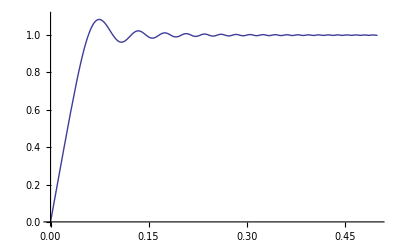

```mathematica
Plot[Sum[coeffs[[i]]Sqrt[x]*BesselJ[1/4,Zeros[[i]]^2*x^2/2],{i,1,160}],{x,0,0.5},PlotRange->{{0,0.5},{0,1.1}}]
```

```mathematica
N[Hypergeometric0F1[1/4,-1/4 BesselJZero[-3/4,2]^2]]
```

-2.65582×10^-15

```mathematica
Integrate[x^(5/2) BesselJ[1/4,x^2/2*Zerostrue[[2]]^2],{x,0,1}]
```

Limit::ztest1: Unable to decide whether numeric quantity Hypergeometric0F1[1/4, -1/4 BesselJZero[-3/4, 2]^2] is equal to zero. Assuming it is.

1/(2^(1/4) BesselJZero[-3/4,2]^(7/4) Gamma[1/4])

```mathematica
NIntegrate[x*BesselJ[1/4,x^2*coeffs[[1]]]*BesselJ[1/4,x^2*coeffs[[2]]],{x,0,1}]
```

0.0714686

```mathematica
N[Integrate[x*BesselJ[1/4,x^2/4]BesselJ[3/4,x^2/4],{x,0,1}]]
```

0.0371135

```mathematica
Integrate[x*BesselJ[1/4,x^2/4],{x,0,1}]
```

(4 2^(1/4) HypergeometricPFQ[{5/8},{5/4,13/8},-1/64])/(5 Gamma[1/4])

```mathematica
N[BesselJ[1/4,1]]
```

0.752231

## Linear Profile

```mathematica
DSolve[y''[x]+y[x]*x==0,y[x],x]
```

{{y[x]→AiryAi[(-1)^(1/3) x] C[1]+AiryBi[(-1)^(1/3) x] C[2]}}

```mathematica
sol1=Sqrt[x]BesselJ[-1/3,2/3m x^(3/2)]
```

√x BesselJ[-1/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[D[sol1,{x,2}]+sol1*x*m^2]
```

0

```mathematica
sol2=Sqrt[x]*BesselJ[1/3,2/3*m*x^(3/2)]
```

√x BesselJ[1/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[D[sol2,{x,2}]+sol2*x*m^2]
```

0

```mathematica
Limit[sol1,x->0]
```

3^(1/3)/(m^(1/3) Gamma[2/3])

```mathematica
Limit[sol2,x->0]
```

0

```mathematica
dersol1=FullSimplify[D[sol1,x]]
```

-m x BesselJ[2/3,2/3 m x^(3/2)]

```mathematica
dersol2=FullSimplify[D[sol2,x]]
```

m x BesselJ[-2/3,2/3 m x^(3/2)]

```mathematica
FullSimplify[Limit[dersol1,x->1]]
```

-(m^(5/3) Hypergeometric0F1Regularized[5/3,-m^2/9])/3^(2/3)

```mathematica
FullSimplify[Limit[dersol2,x->1]]
```

3^(2/3) m^(1/3) Hypergeometric0F1Regularized[1/3,-m^2/9]

```mathematica
Limit[dersol2,x->1]
```

1/2 m^(1/3) (-3 AiryAiPrime[-m^(2/3)]+√3 AiryBiPrime[-m^(2/3)])

```mathematica
Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m>0},m]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m>0},m]

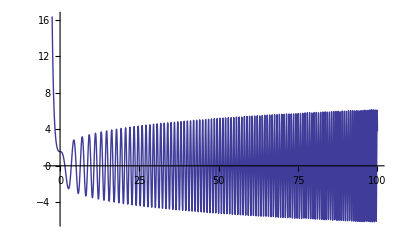

```mathematica
Plot[-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x],{x,-3,100}]
```

```mathematica
Reduce[{-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x]},x,Reals]
```

Reduce::naqs: And[-3 AiryAiPrime[-x] + √3 AiryBiPrime[-x]] is not a quantified system of equations and inequalities.

```mathematica
FindRoot[{-3 AiryAiPrime[-x]+√3 AiryBiPrime[-x]==0},{x,7}]
```

{x→17.4104}

```mathematica
Reduce[{Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m]
```

Reduce::nsmet: This system cannot be solved with the methods available to Reduce.

Reduce[Hypergeometric0F1Regularized[1/3,-m^2/9]==0,m]

```mathematica
FullSimplify[Hypergeometric0F1[1/3,x]]
```

```mathematica
FunctionExpand[Hypergeometric0F1[a,-m^2/9]]
```

3^(-1+a) m^(1-a) BesselJ[-1+a,(2 m)/3] Gamma[a]

```mathematica
N[BesselJZero[-2/3,1]]
```

1.24305

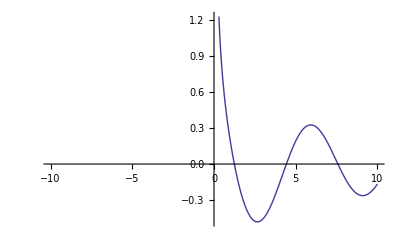

```mathematica
Plot[BesselJ[-2/3,x],{x,-10,10}]
```

```mathematica
FullSimplify[D[BesselJ[0,x^2]+2x^2BesselJ[0,x^2],{x,2}]]
```

-4 (-1+x^2+2 x^4) BesselJ[0,x^2]+2 (1-6 x^2) BesselJ[1,x^2]

```mathematica
oldtest=√x BesselJ[1/4,(m^2 x^2)/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
FullSimplify[D[oldtest,{x,2}]+m^4 x^2 oldtest]
```

0

## Checking solution

```mathematica
y1=Sqrt[x]BesselJ[1/4,m^2 x^2/2]
```

√x BesselJ[1/4,(m^2 x^2)/2]

```mathematica
y2=Sqrt[x]BesselJ[-1/4,m^2 x^2/2]
```

√x BesselJ[-1/4,(m^2 x^2)/2]

```mathematica
FullSimplify[D[y1,{x,2}]+m^4 x^2 y1]
```

0

```mathematica
FullSimplify[D[y2,{x,2}]+m^4 x^2 y2]
```

0

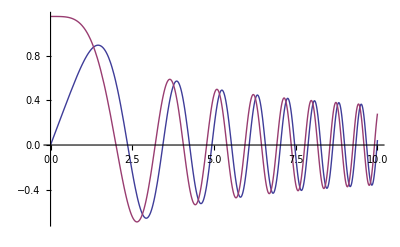

```mathematica
Plot[{y1/.{m->1},y2/.{m->1}},{x,0,10}]
```

```mathematica
Limit[y1,x->0]
```

0

```mathematica
Limit[y2,x->0]
```

(√2 (m^2)^(3/4))/(m^2 Gamma[3/4])

```mathematica
y1prime=FullSimplify[D[y1,x]]
```

m^2 x^(3/2) BesselJ[-3/4,(m^2 x^2)/2]

```mathematica
y2prime=FullSimplify[D[y2,x]]
```

-m^2 x^(3/2) BesselJ[3/4,(m^2 x^2)/2]

```mathematica
y1primezeros=Table[N[Sqrt[2*BesselJZero[-3/4,i]],20],{i,1,600}]
```

{1.4549970854981938672,2.9271330044002777036,3.8575781013492938202,4.6017777322812998532,5.2408240669907031435,5.8097878642639890649,6.3276943010839668153,6.806248002251421267,7.2532616896568630882,7.6742592995607184149,8.0733179531910894634,8.4535489743734023316,8.8173908688408068047,9.1667970236322875122,9.5033609889776088707,9.8284029864744712644,10.143031377122199112,10.448187418116219834,10.744678548081275731,11.033203602582975389,11.314372229981451421,11.588720059406771191,11.856720704520474493,12.118795374381111674,12.375320649886455888,12.626634836450731272,12.87304319914884181,13.114822311627388636,13.352223695543593481,13.585476887076649348,13.814792037042309787,14.040362128492540369,14.262364878414205497,14.48096437684933246,14.696312506437453834,14.908550177297680534,15.11780840578937571,15.324209260619499952,15.527866695705965984,15.728887285936653644,15.927370879313617345,16.123411176811677537,16.31709624950989468,16.508509001095592351,16.697727582632798065,16.884825765482342392,17.069873277421512249,17.252936106306933187,17.434076775031120724,17.613354591021474801,17.790825873104697492,17.966544158196943431,18.140560389970064199,18.31292309137856038,18.483678522703297299,18.652870826570881769,18.820542161237036456,18.986732823274350716,19.151481360676095919,19.31482467727557424,19.476798129282373383,19.63743561465094432,19.796769655921429725,19.954831477106225805,20.11165107513715108,20.26725728633629104,20.421677848327705924,20.574939457766473983,20.727067824225345009,20.878087720547038679,21.028023029941456202,21.176896790081363557,21.324731234427087406,21.471547830990125379,21.617367318727036134,21.762209741738301831,21.90609448143183688,22.04904028679726849,22.191065302924875575,22.332187097892001451,22.472422688129727631,22.611788562373501071,22.750300704293148089,22.887974613890198985,23.024825327743611767,23.160867438178753771,23.29611511142881612,23.430582104852644309,23.56428178326822106,23.697227134456692222,23.829430783887844841,23.960905008714294482,24.091661751078285785,24.22171263077192876,24.351068957288858703,24.479741741302697704,24.607741705605290585,24.735079295535469626,24.861764688927054501,24.987807805602901584,25.113218316440067089,25.238005652029529168,25.362179010952414348,25.485747367693283491,25.608719480209742988,25.731103897176449771,25.852908964920466715,25.974142834063891146,26.094813465888717411,26.214928638437999102,26.334495952366542442,26.453522836553584793,26.572016553489186973,26.689984204445391069,26.807432734442563151,26.924368937020749386,27.040799458825321449,27.156730804015670103,27.272169338505221757,27.387121294040599319,27.501592772127323684,27.615589747809053542,27.729118073306987232,27.842183481525699181,27.954791589431353672,28.066947901307928685,28.178657811896791086,28.289926609424690236,28.400759478524978996,28.511161503056628065,28.621137668825370615,28.730692866211098355,28.839831892705426618,28.948559455363154065,29.056880173171161341,29.164798579338121888,29.272319123508236432,29.379446173902049873,29.486184019387264817,29.592536871482329341,29.698508866295447279,29.804104066401536864,29.909326462659547666,30.014179975972435904,30.118668458991994113,30.222795697770632452,30.326565413362115304,30.42998126337316801,30.53304684346778425,30.635765688825984515,30.738141275558700088,30.840177022080384674,30.941876290440887128,31.043242387618053442,31.144278566772464013,31.244988028465653091,31.345373921843101088,31.445439345783236817,31.545187350013635746,31.64462093619555173,31.74374305897787337,31.842556627021551983,31.941064503995506074,32.039269509544967017,32.137174420233192332,32.234781970457436379,32.332094853340033339,32.429115721595414037,32.525847188373846267,32.622291828082657874,32.718452177185672715,32.814330734981561846,32.909929964361785633,33.0052522925487771,33.100300111814992409,33.195075780183431143,33.289581622110206695,33.383819929149725749,33.477792960603015357,33.571502944149716543,33.664952076464244561,33.75814252381659796,33.85107642265828133,33.943755880193790077,34.036182974938089685,34.128359757260506712,34.220288249915434154,34.311970448560239769,34.403408322260752517,34.494603813984689324,34.585558841083371975,34.676275295762071994,34.766755045539309931,34.856999933695424453,34.947011779710716029,35.036792379693459849,35.12634350679807281,35.215666911633709988,35.304764322663556952,35.393637446595075573,35.482287968761452567,35.570717553494491975,35.658927844489184953,35.746920465160182812,35.834697018990391998,35.922259089871902771,36.00960824243945665,36.096746022396651224,36.183673956835074742,36.270393554546556847,36.356906306328716117,36.443213685283979415,36.529317147112242741,36.615218130397338062,36.700918056887465594,36.786418331769746174,36.871720343939043727,36.95682546626120329,37.041735055830845739,37.126450454223856172,37.210972987744698812,37.295303967668687431,37.379444690479336467,37.463396438100914373,37.547160478126317209,37.630738064040377055,37.714130435438716538,37.797338818242257561,37.880364424907489255,37.963208454632597161,38.045872093559552783,38.128356514972259859,38.210662879490850973,38.292792335262225543,38.374746018146917655,38.4565250519023798,38.538130548362766158,38.619563607615296808,38.70082531817328199,38.781916757145883415,38.862838990404687505,38.943593072747163446,39.024180048057076954,39.10460094946192878,39.184856799487485107,39.264948610209465236,39.344877383402450217,39.42464411068607439,39.504249773668560201,39.583695344087655055,39.662981783949027455,39.742110045662178181,39.821081072173920821,39.899895797099484588,39.978555144851290971,40.057060030765454476,40.135411361226056423,40.213610033787239526,40.291656937293169788,40.369552951995911058,40.447298949671256469,40.524895793732559889,40.602344339342609406,40.679645433523583879,40.756799915265132522,40.833808615630616558,40.910672357861550979,40.987391957480283553,41.063968222390947308,41.140401952978721825,41.216693942207437862,41.292844975715558969,41.368855831910572943,41.444727282061825237,41.520460090391825608,41.596055014166058602,41.67151280378132772,41.746834202852662431,41.822019948298816494,41.897070770426385398,41.971987393012570091,42.046770533386613512,42.121420902509935866,42.195939205054993951,42.270326139482889284,42.34458239811974921,42.41870866723190461,42.492705627099887317,42.56657395209126979,42.640314310732369125,42.713927365778836963,42.787413774285156373,42.860774187673066339,42.934009251798933998,43.007119607020094334,43.080105888260176618,43.152968725073436434,43.225708741708111739,43.298326557168820975,43.370822785278020902,43.443198034736541394,43.515452909183214087,43.587588007253611409,43.659603922637912159,43.731501244137909453,43.803280555723176522,43.874942436586405526,43.946487461197934206,44.017916199359474905,44.08922921625706016,44.160427072513218803,44.231510324238396171,44.302479523081631781,44.373335216280507535,44.444077946710379238,44.514708252932903966,44.585226669243875547,44.655633725720380186,44.725929948267283991,44.796115858663063945,44.866191974604993612,44.93615880975369466,45.006016873777065028,45.075766672393594379,45.145408707415077244,45.214943476788734066,45.28437147463875014,45.353693191307242257,45.422909113394662658,45.49201972379964971,45.561025501758334545,45.629926922883112704,45.698724459200889664,45.767418579190808945,45.836009747821471331,45.904498426587653564,45.972885073546534712,46.041170143353438268,46.109354087297097852,46.177437353334454265,46.245420386124991478,46.313303627064619008,46.381087514319107977,46.448772482857088025,46.516358964482612096,46.583847387867296004,46.651238178582039546,46.718531759128335788,46.785728548969175057,46.852828964559550021,46.919833419376568141,46.986742323949177646,47.053556085887513079,47.120275109911866355,47.186899797881289142,47.253430548821832295,47.319867758954427949,47.386211821722419784,47.45246312781874688,47.518622065212786457,47.584689019176860737,47.650664372312413041,47.716548504575858148,47.782341793304111864,47.84804461323980465,47.913657336556184077,47.979180332881710782,48.044613969324352531,48.109958610495580904,48.175214618534075032,48.24038235312913676,48.305462171543821498,48.370454428637788986,48.435359476889878099,48.500177666420409754,48.564909345013221913,48.629554858137440604,48.694114548968990815,48.758588758411851046,48.822977825119055258,48.887282085513445852,48.951501873808181299,49.015637522027001954,49.079689360024257511,49.143657715504699542,49.207542914043042464,49.271345279103296238,49.335065132057874052,49.398702792206478179,49.462258576794767143,49.525732801032807296,49.589125778113311822,49.652437819229670166,49.715669233593770825,49.778820328453620375,49.841891409110761589,49.904882778937493434,49.96779473939389569,50.030627590044660894,50.093381628575736278,50.156057150810778305,50.218654450727422374,50.281173820473370236,50.343615550382297605,50.405979928989584415,50.468267243047870126,50.530477777542436468,50.592611815706419945,50.654669639035856394,50.716651527304559867,50.778557758578838063,50.840388609232046483,50.902144353958983486,50.963825265790128342,51.025431616105724396,51.086963674649709371,51.148421709543494854,51.209805987299596947,51.27111677283512004,51.332354329485095643,51.393518919015678172,51.454610801637199561,51.515630236017084542,51.576577479292628405,51.637452787083639026,51.698256413504944915,51.758988611178771022,51.819649631246984008,51.880239723383208646,51.940759135804817023,52.001208115284792159,52.061586907163467655,52.121895755360144939,52.182134902384589683,52.242304589348408905,52.302405055976310282,52.362436540617245147,52.422399280255436646,52.482293510521294495,52.542119465702217755,52.601877378753287031,52.661567481307847475,52.721190003687983949,52.780745174914889692,52.840233222719129806,52.899654373550800875,52.959008852589587978,53.01829688375472038,53.077518689714827134,53.136674491897693827,53.195764510499921669,53.254788964496490136,53.313748071650224321,53.372642048521168167,53.431471110475864707,53.490235471696544455,53.548935345190223042,53.607570942797709197,53.666142475202524146,53.724650151939733494,53.783094181404692644,53.84147477086170677,53.899792126452606374,53.958046453205239429,54.016237955041881094,54.074366834787561978,54.132433294178315919,54.190437533869348217,54.248379753443125271,54.306260151417386527,54.364078925253079662,54.421836271362219883,54.479532385115674248,54.537167460850871859,54.594741691879440808,54.652255270494772711,54.709708387979515667,54.767101234612996486,54.824433999678572971,54.881706871470917088,54.938920037303229796,54.996073683514388322,55.053167995476026668,55.110203157599550084,55.167179353343084286,55.224096765218360136,55.280955574797534535,55.337755962719948234,55.394498108698821282,55.451182191527886814,55.507808389087963866,55.564376878353469911,55.620887835398873772,55.677341435405089601,55.73373785266581256,55.79007726059379687,55.846359831727076845,55.902585737735131569,55.958755149424993824,56.014868236747303873,56.070925168802308737,56.126926113845807533,56.182871239295043477,56.238760711734543145,56.294594696921903546,56.350373359793527601,56.406096864470308569,56.461765374263263982,56.517379051679119641,56.5729380584258442,56.628442555418134893,56.683892702782854897,56.73928865986442289,56.794630585230155285,56.849918636675561662,56.9051529712295939,56.96033374515984949,57.01546111397772953,57.070535232443551883,57.125556254571619958,57.180524333635247601,57.235439622171740558,57.290302271987334954,57.345112434162093254,57.399870259054758153,57.45457589630756482,57.509229494851011954,57.563831202908592067,57.618381168001481421,57.672879536953190044,57.727326455894172239,57.781722070266397985,57.836066524827885653,57.890359963657196417,57.944602530157890768,57.998794367062947521,58.052935616439145689,58.107026419691409614,58.161066917567117729,58.215057250160375324,58.268997556916251677,58.322887976634981918,58.376728647476133982,58.430519706962741007,58.484261291985399519,58.537953538806333768,58.591596583063426525,58.645190559774216716,58.69873560333986419,58.752231847549081975,58.805679425582036338,58.859078470014214967,58.912429112820263608,58.965731485377791444,59.018985718471145559,59.072191942295154768,59.125350286458843127,59.178460879989113424,59.231523851334400944,59.284539328368297797,59.337507438393148104,59.390428308143614332,59.443302063790215043,59.496128830942834354,59.548908734654203375,59.601641899423353903,59.654328449199044632,59.706968507383160163,59.759562196834083059,59.812109639870039217,59.864610958272416813,59.917066273289059071,59.969475705637531111,60.021839375508361124,60.074157402568256126,60.126429905963292516,60.178657004322081706,60.230838815758911034,60.282975457876860216,60.33506704777089356,60.387113702030928165,60.439115536744878354,60.491072667501676539,60.542985209394270763,60.594853277022599127,60.646676984496541319,60.698456445438847467,60.750191772988044523,60.801883079801320391,60.853530478057386005,60.905134079459315561,60.956693995237365117,61.008210336151769745,61.059683212495519451,61.111112734097114045,61.162499010323297165,61.213842150081769653,61.265142261823882449,61.316399453547309227,61.367613832798698922}

```mathematica
wmcubic=Table[NIntegrate[x^3 BesselJ[1/4,x^2/2*y1primezeros[[i]]^2]^2,{x,0,1}],{i,1,600}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9316561666405324`}. NIntegrate obtained 0.000216152 and 2.44826×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9316250833594676`}. NIntegrate obtained 0.000215234 and 2.57691×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9355624166405324`}. NIntegrate obtained 0.000214323 and 2.47135×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{0.137974,0.0368546,0.0213316,0.0150107,0.0115796,0.00942524,0.00794677,0.00686924,0.00604903,0.0054038,0.00488295,0.00445368,0.00409379,0.00378771,0.00352422,0.003295,0.00309378,0.00291572,0.00275704,0.00261474,0.00248641,0.00237009,0.00226416,0.0021673,0.00207838,0.00199648,0.00192078,0.00185062,0.0017854,0.00172462,0.00166784,0.00161468,0.00156481,0.00151792,0.00147376,0.0014321,0.00139273,0.00135547,0.00132015,0.00128662,0.00125475,0.00122443,0.00119553,0.00116797,0.00114165,0.00111649,0.00109241,0.00106935,0.00104725,0.00102604,0.00100567,0.000986094,0.000967267,0.000949145,0.000931689,0.000914864,0.000898636,0.000882973,0.000867847,0.000853231,0.000839099,0.000825427,0.000812194,0.000799378,0.000786961,0.000774923,0.000763248,0.00075192,0.000740923,0.000730243,0.000719866,0.000709781,0.000699974,0.000690434,0.000681151,0.000672114,0.000663314,0.000654741,0.000646387,0.000638244,0.000630303,0.000622557,0.000615,0.000607623,0.000600422,0.000593389,0.000586519,0.000579806,0.000573246,0.000566832,0.00056056,0.000554425,0.000548423,0.00054255,0.000536801,0.000531173,0.000525661,0.000520263,0.000514974,0.000509792,0.000504713,0.000499735,0.000494853,0.000490066,0.000485371,0.000480765,0.000476245,0.00047181,0.000467456,0.000463183,0.000458986,0.000454865,0.000450817,0.000446841,0.000442934,0.000439095,0.000435322,0.000431613,0.000427967,0.000424382,0.000420856,0.000417389,0.000413978,0.000410623,0.000407321,0.000404073,0.000400875,0.000397728,0.00039463,0.000391579,0.000388576,0.000385618,0.000382705,0.000379836,0.000377009,0.000374224,0.00037148,0.000368776,0.000366111,0.000363484,0.000360895,0.000358342,0.000355825,0.000353343,0.000350896,0.000348482,0.000346101,0.000343753,0.000341436,0.00033915,0.000336895,0.000334669,0.000332473,0.000330305,0.000328166,0.000326054,0.000323969,0.00032191,0.000319877,0.00031787,0.000315888,0.000313931,0.000311997,0.000310088,0.000308201,0.000306338,0.000304496,0.000302677,0.00030088,0.000299103,0.000297348,0.000295612,0.000293898,0.000292202,0.000290527,0.00028887,0.000287232,0.000285613,0.000284012,0.000282428,0.000280863,0.000279314,0.000277783,0.000276268,0.000274769,0.000273287,0.000271821,0.00027037,0.000268935,0.000267515,0.000266109,0.000264719,0.000263343,0.000261981,0.000260633,0.000259299,0.000257979,0.000256672,0.000255378,0.000254097,0.000252829,0.000251573,0.00025033,0.000249099,0.000247881,0.000246674,0.000245478,0.000244295,0.000243122,0.000241961,0.000240811,0.000239672,0.000238543,0.000237425,0.000236318,0.00023522,0.000234133,0.000233056,0.000231989,0.000230931,0.000229884,0.000228845,0.000227816,0.000226796,0.000225785,0.000224784,0.000223791,0.000222806,0.000221831,0.000220864,0.000219905,0.000218954,0.000218012,0.000217078,0.000216152,0.000215234,0.000214323,0.00021342,0.000212525,0.000211637,0.000210756,0.000209883,0.000209017,0.000208159,0.000207307,0.000206462,0.000205624,0.000204793,0.000203968,0.00020315,0.000202339,0.000201534,0.000200735,0.000199943,0.000199157,0.000198377,0.000197603,0.000196836,0.000196074,0.000195318,0.000194568,0.000193823,0.000193085,0.000192352,0.000191624,0.000190902,0.000190185,0.000189474,0.000188768,0.000188067,0.000187372,0.000186681,0.000185996,0.000185315,0.00018464,0.000183969,0.000183304,0.000182643,0.000181987,0.000181335,0.000180689,0.000180047,0.000179409,0.000178776,0.000178147,0.000177523,0.000176903,0.000176287,0.000175676,0.000175069,0.000174466,0.000173867,0.000173273,0.000172682,0.000172095,0.000171513,0.000170934,0.000170359,0.000169788,0.000169221,0.000168658,0.000168098,0.000167542,0.00016699,0.000166441,0.000165896,0.000165355,0.000164817,0.000164282,0.000163103,0.000163224,0.0001627,0.000162179,0.000161661,0.000161147,0.000160636,0.000160128,0.000159624,0.000159122,0.000158624,0.000158129,0.000157637,0.000157148,0.000156662,0.000156179,0.000155699,0.000155222,0.000154748,0.000154277,0.000153808,0.000153343,0.00015288,0.00015242,0.000151963,0.000151508,0.000151057,0.000150607,0.000150161,0.000149717,0.000149276,0.000148838,0.000148402,0.000147968,0.000147537,0.000147111,0.000146683,0.000146259,0.000145838,0.00014542,0.000145003,0.00014459,0.000144178,0.000143769,0.000143362,0.000142958,0.000142555,0.000142155,0.000141758,0.000141362,0.000140969,0.000140577,0.000140188,0.000139802,0.000139417,0.000139034,0.000138654,0.000138275,0.000137899,0.000137525,0.000137152,0.000136782,0.000136414,0.000136047,0.000135683,0.00013532,0.00013496,0.000134601,0.000134245,0.00013389,0.000133537,0.000133186,0.000132837,0.000132489,0.000132144,0.0001318,0.000131458,0.000131118,0.000130779,0.000130442,0.000130107,0.000129774,0.000129438,0.000129113,0.000128784,0.000128458,0.000128133,0.00012781,0.000127488,0.000127168,0.000126849,0.000126533,0.000126218,0.000125904,0.000125592,0.000125281,0.000124972,0.000124665,0.000124359,0.000124054,0.000123751,0.00012345,0.000123149,0.000122851,0.000122554,0.000122258,0.000121964,0.000121671,0.000121379,0.000121089,0.0001208,0.000120785,0.000120227,0.000119942,0.000119659,0.000119377,0.000119096,0.000118817,0.000118539,0.000118262,0.000117987,0.000117687,0.00011744,0.000117168,0.000116906,0.000116629,0.000116361,0.000115931,0.00011582,0.000115565,0.000115301,0.00011504,0.000114779,0.000114519,0.000114261,0.000114004,0.000113748,0.000113493,0.000113246,0.000112986,0.000112736,0.000112486,0.000112236,0.000111988,0.000111741,0.000111495,0.00011125,0.000111007,0.000110777,0.000110522,0.000110282,0.000110036,0.000109804,0.000109566,0.000109216,0.000109013,0.000108883,0.000108626,0.000108394,0.000108162,0.000107932,0.000107703,0.000107474,0.000107165,0.000107025,0.000106794,0.000106573,0.000106346,0.000106123,0.000105901,0.000105668,0.000105994,0.000105468,0.000105023,0.000104388,0.000104457,0.000104374,0.000104044,0.000103946,0.000103711,0.000103521,0.000103321,0.000103099,0.00010289,0.000101219,0.000102474,0.00010208,0.000101687,0.000102051,0.000102021,0.000101414,0.000101018,0.000101043,0.000100219,0.000100754,0.000100541,0.00010006,0.000100127,0.0000988969,0.0000994977,0.0000986825,0.000099256,0.0000990632,0.0000989961,0.0000980233,0.0000984896,0.0000986385,0.000098308,0.0000981183,0.0000975033,0.0000975149,0.0000974979,0.0000971879,0.00009646,0.0000973384,0.0000966114,0.000096425,0.0000966143,0.0000965375,0.0000958753,0.0000958157,0.0000953643,0.0000955268,0.000095263,0.0000943072,0.0000949373,0.0000925127,0.0000940131,0.0000946417,0.0000937628,0.0000940243,0.0000937468,0.0000926296,0.0000934641,0.0000932872,0.0000935235,0.0000921912,0.0000928578,0.0000932318,0.00009233,0.0000921343,0.000092283,0.0000920032,0.0000919019,0.0000917019,0.00009184,0.0000919161,0.0000901463,0.0000909306,0.0000905815,0.0000905242,0.00009051,0.0000909176,0.000089796,0.0000899604,0.0000895464,0.0000888033,0.000089889,0.0000892798,0.0000890192,0.0000894793,0.000090114,0.0000890121,0.0000878674,0.0000885816,0.0000888411,0.0000878179,0.0000882411,0.0000882331,0.0000855093,0.0000876056,0.0000891957,0.0000873522,0.0000882287,0.0000869635,0.0000870036,0.0000874479,0.0000861414,0.0000862678,0.000086099,0.0000862865,0.0000861084,0.0000859316,0.0000866446,0.0000844685,0.0000853553,0.0000854001,0.000082701,0.0000837479,0.0000854777,0.0000838604}

```mathematica
NIntegrate[x^(5/2)* BesselJ[1/4,x^2/2*y1primezeros[[1]]^2],{x,0,1}]
```

Part::partd: Part specification y1primezeros ⟦ 1 ⟧ is longer than depth of object.

NIntegrate::inumr: The integrand x^5/2 BesselJ[1/4, 1/2 x^2 y1primezeros ⟦ 1 ⟧^2] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[x^(5/2) BesselJ[1/4,1/2 x^2 y1primezeros⟦1⟧^2],{x,0,1}]

```mathematica
wmfivetwo=Table[NIntegrate[x^(5/2)* BesselJ[1/4,x^2/2*y1primezeros[[i]]^2],{x,0,1}],{i,1,600}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9355313333594676`}. NIntegrate obtained 3.01015×10^-6 and 3.32518×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9355313333594676`}. NIntegrate obtained 2.98365×10^-6 and 3.20063×10^-12 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.9316561666405324`}. NIntegrate obtained 2.95751×10^-6 and 3.51276×10^-12 for the integral and error estimates.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

{0.209965,0.0181809,0.0069193,0.00373185,0.00236737,0.00165045,0.00122407,0.000948389,0.000759097,0.000623069,0.000521773,0.000444147,0.000383242,0.000334505,0.000294845,0.000262104,0.000234734,0.000211602,0.000191861,0.000174867,0.000160124,0.000147245,0.000135921,0.000125909,0.000117008,0.000109058,0.000101925,0.0000954983,0.0000896863,0.0000844115,0.0000796084,0.0000752211,0.0000712022,0.0000675107,0.0000641113,0.0000609733,0.0000580702,0.0000553784,0.0000528777,0.00005055,0.0000483793,0.0000463516,0.0000444543,0.0000426763,0.0000410075,0.000039439,0.0000379628,0.0000365716,0.0000352588,0.0000340186,0.0000328456,0.000031735,0.0000306822,0.0000296833,0.0000287346,0.0000278326,0.0000269744,0.000026157,0.0000253779,0.0000246346,0.000023925,0.000023247,0.0000225987,0.0000219784,0.0000213844,0.0000208152,0.0000202695,0.000019746,0.0000192434,0.0000187606,0.0000182966,0.0000178503,0.0000174209,0.0000170076,0.0000166094,0.0000162257,0.0000158557,0.0000154989,0.0000151545,0.0000148219,0.0000145007,0.0000141903,0.0000138902,0.0000136,0.0000133192,0.0000130473,0.0000127841,0.0000125292,0.0000122821,0.0000120427,0.0000118104,0.0000115852,0.0000113666,0.0000111544,0.0000109484,0.0000107483,0.0000105539,0.000010365,0.0000101813,0.0000100027,9.82892×10^-6,9.65987×10^-6,9.49535×10^-6,9.33519×10^-6,9.17923×10^-6,9.02733×10^-6,8.87935×10^-6,8.73514×10^-6,8.59457×10^-6,8.45753×10^-6,8.32389×10^-6,8.19354×10^-6,8.06637×10^-6,7.94227×10^-6,7.82115×10^-6,7.70291×10^-6,7.58745×10^-6,7.47468×10^-6,7.36453×10^-6,7.25691×10^-6,7.15174×10^-6,7.04894×10^-6,6.94845×10^-6,6.85019×10^-6,6.75409×10^-6,6.6601×10^-6,6.56815×10^-6,6.47817×10^-6,6.39012×10^-6,6.30394×10^-6,6.21956×10^-6,6.13695×10^-6,6.05605×10^-6,5.97681×10^-6,5.89919×10^-6,5.82314×10^-6,5.74862×10^-6,5.67559×10^-6,5.60401×10^-6,5.53384×10^-6,5.46503×10^-6,5.39756×10^-6,5.33139×10^-6,5.26649×10^-6,5.20282×10^-6,5.14035×10^-6,5.07905×10^-6,5.01889×10^-6,4.95985×10^-6,4.90189×10^-6,4.84498×10^-6,4.78911×10^-6,4.73424×10^-6,4.68036×10^-6,4.62743×10^-6,4.57544×10^-6,4.52436×10^-6,4.47417×10^-6,4.42484×10^-6,4.37637×10^-6,4.32873×10^-6,4.2819×10^-6,4.23585×10^-6,4.19059×10^-6,4.14607×10^-6,4.1023×10^-6,4.05925×10^-6,4.0169×10^-6,3.97524×10^-6,3.93426×10^-6,3.89394×10^-6,3.85426×10^-6,3.81522×10^-6,3.77679×10^-6,3.73897×10^-6,3.70174×10^-6,3.66509×10^-6,3.62901×10^-6,3.59348×10^-6,3.55849×10^-6,3.52404×10^-6,3.49011×10^-6,3.45669×10^-6,3.42377×10^-6,3.39134×10^-6,3.35939×10^-6,3.32791×10^-6,3.29689×10^-6,3.26632×10^-6,3.2362×10^-6,3.20651×10^-6,3.17724×10^-6,3.1484×10^-6,3.11996×10^-6,3.09192×10^-6,3.06428×10^-6,3.03703×10^-6,3.01015×10^-6,2.98365×10^-6,2.95751×10^-6,2.93173×10^-6,2.9063×10^-6,2.88121×10^-6,2.85646×10^-6,2.83205×10^-6,2.80796×10^-6,2.78419×10^-6,2.76074×10^-6,2.7376×10^-6,2.71476×10^-6,2.69221×10^-6,2.66997×10^-6,2.648×10^-6,2.62632×10^-6,2.60492×10^-6,2.58379×10^-6,2.56293×10^-6,2.54233×10^-6,2.522×10^-6,2.50191×10^-6,2.48208×10^-6,2.46249×10^-6,2.44314×10^-6,2.42404×10^-6,2.40516×10^-6,2.38652×10^-6,2.3681×10^-6,2.3499×10^-6,2.33192×10^-6,2.31416×10^-6,2.29661×10^-6,2.27927×10^-6,2.26213×10^-6,2.2452×10^-6,2.22846×10^-6,2.21192×10^-6,2.19557×10^-6,2.17941×10^-6,2.16343×10^-6,2.14764×10^-6,2.13203×10^-6,2.1166×10^-6,2.10134×10^-6,2.08625×10^-6,2.07133×10^-6,2.05658×10^-6,2.042×10^-6,2.02757×10^-6,2.01331×10^-6,1.9992×10^-6,1.98525×10^-6,1.97145×10^-6,1.9578×10^-6,1.9443×10^-6,1.93094×10^-6,1.91773×10^-6,1.90466×10^-6,1.89173×10^-6,1.87893×10^-6,1.86627×10^-6,1.85375×10^-6,1.84135×10^-6,1.82909×10^-6,1.81695×10^-6,1.80494×10^-6,1.79306×10^-6,1.78129×10^-6,1.76965×10^-6,1.75813×10^-6,1.74672×10^-6,1.73543×10^-6,1.72426×10^-6,1.71319×10^-6,1.70224×10^-6,1.6914×10^-6,1.68067×10^-6,1.67004×10^-6,1.65952×10^-6,1.6491×10^-6,1.63878×10^-6,1.62857×10^-6,1.61845×10^-6,1.60843×10^-6,1.59851×10^-6,1.58869×10^-6,1.57896×10^-6,1.56932×10^-6,1.55978×10^-6,1.55033×10^-6,1.54096×10^-6,1.53169×10^-6,1.5225×10^-6,1.5134×10^-6,1.50438×10^-6,1.49545×10^-6,1.4866×10^-6,1.47784×10^-6,1.46915×10^-6,1.46055×10^-6,1.45202×10^-6,1.44357×10^-6,1.4352×10^-6,1.4269×10^-6,1.41868×10^-6,1.41053×10^-6,1.40246×10^-6,1.39446×10^-6,1.38653×10^-6,1.37867×10^-6,1.37088×10^-6,1.36316×10^-6,1.35551×10^-6,1.34793×10^-6,1.34041×10^-6,1.33295×10^-6,1.32557×10^-6,1.31824×10^-6,1.31098×10^-6,1.30379×10^-6,1.29665×10^-6,1.28958×10^-6,1.28256×10^-6,1.27561×10^-6,1.26871×10^-6,1.26188×10^-6,1.2551×10^-6,1.24837×10^-6,1.24171×10^-6,1.2351×10^-6,1.22854×10^-6,1.22204×10^-6,1.2156×10^-6,1.2092×10^-6,1.20286×10^-6,1.19658×10^-6,1.19034×10^-6,1.18415×10^-6,1.17802×10^-6,1.17193×10^-6,1.1659×10^-6,1.15991×10^-6,1.15397×10^-6,1.14808×10^-6,1.14223×10^-6,1.13643×10^-6,1.13068×10^-6,1.12497×10^-6,1.11931×10^-6,1.1137×10^-6,1.10812×10^-6,1.1026×10^-6,1.09711×10^-6,1.09167×10^-6,1.08627×10^-6,1.08091×10^-6,1.07559×10^-6,1.07031×10^-6,1.06508×10^-6,1.05988×10^-6,1.05473×10^-6,1.04961×10^-6,1.04453×10^-6,1.03949×10^-6,1.03449×10^-6,1.02953×10^-6,1.0246×10^-6,1.01972×10^-6,1.01486×10^-6,1.01005×10^-6,1.00527×10^-6,1.00052×10^-6,9.95811×10^-7,9.91136×10^-7,9.86495×10^-7,9.81889×10^-7,9.77316×10^-7,9.72776×10^-7,9.6827×10^-7,9.63796×10^-7,9.59354×10^-7,9.54945×10^-7,9.50567×10^-7,9.46221×10^-7,9.41906×10^-7,9.37622×10^-7,9.33368×10^-7,9.29145×10^-7,9.24951×10^-7,9.20788×10^-7,9.16653×10^-7,9.12548×10^-7,9.08472×10^-7,9.04424×10^-7,9.00404×10^-7,8.96412×10^-7,8.92448×10^-7,8.88512×10^-7,8.84603×10^-7,8.8072×10^-7,8.76865×10^-7,8.73036×10^-7,8.69233×10^-7,8.65456×10^-7,8.61705×10^-7,8.57979×10^-7,8.54279×10^-7,8.50603×10^-7,8.46953×10^-7,8.43326×10^-7,8.39725×10^-7,8.36147×10^-7,8.32593×10^-7,8.29063×10^-7,8.25557×10^-7,8.22073×10^-7,8.18613×10^-7,8.15175×10^-7,8.11761×10^-7,8.08368×10^-7,8.04998×10^-7,8.0165×10^-7,7.98323×10^-7,7.95019×10^-7,7.91735×10^-7,7.88473×10^-7,7.85233×10^-7,7.82012×10^-7,7.78813×10^-7,7.75634×10^-7,7.72476×10^-7,7.69337×10^-7,7.66219×10^-7,7.63121×10^-7,7.60042×10^-7,7.56982×10^-7,7.53942×10^-7,7.50921×10^-7,7.47919×10^-7,7.44936×10^-7,7.41972×10^-7,7.39026×10^-7,7.36098×10^-7,7.33189×10^-7,7.30297×10^-7,7.27424×10^-7,7.24568×10^-7,7.21729×10^-7,7.18909×10^-7,7.16105×10^-7,7.13319×10^-7,7.10549×10^-7,7.07797×10^-7,7.05061×10^-7,7.02342×10^-7,6.99639×10^-7,6.96952×10^-7,6.94282×10^-7,6.91628×10^-7,6.88989×10^-7,6.86367×10^-7,6.8376×10^-7,6.81169×10^-7,6.78593×10^-7,6.76032×10^-7,6.73486×10^-7,6.70956×10^-7,6.6844×10^-7,6.65939×10^-7,6.63453×10^-7,6.60981×10^-7,6.58524×10^-7,6.56081×10^-7,6.53653×10^-7,6.51238×10^-7,6.48838×10^-7,6.46451×10^-7,6.44078×10^-7,6.41719×10^-7,6.39377×10^-7,6.37041×10^-7,6.34722×10^-7,6.32416×10^-7,6.30124×10^-7,6.27844×10^-7,6.25578×10^-7,6.23324×10^-7,6.21083×10^-7,6.18854×10^-7,6.16639×10^-7,6.14435×10^-7,6.12244×10^-7,6.10065×10^-7,6.07899×10^-7,6.05744×10^-7,6.03602×10^-7,6.01472×10^-7,5.99352×10^-7,5.97245×10^-7,5.95149×10^-7,5.93065×10^-7,5.90992×10^-7,5.88931×10^-7,5.86881×10^-7,5.84842×10^-7,5.82815×10^-7,5.80798×10^-7,5.78792×10^-7,5.76797×10^-7,5.74813×10^-7,5.7284×10^-7,5.70877×10^-7,5.68925×10^-7,5.66983×10^-7,5.65052×10^-7,5.63131×10^-7,5.6122×10^-7,5.5932×10^-7,5.57429×10^-7,5.55549×10^-7,5.53678×10^-7,5.51818×10^-7,5.49967×10^-7,5.48126×10^-7,5.46294×10^-7,5.44472×10^-7,5.4266×10^-7,5.40857×10^-7,5.39064×10^-7,5.3728×10^-7,5.35505×10^-7,5.33739×10^-7,5.31982×10^-7,5.30235×10^-7,5.28496×10^-7,5.26767×10^-7,5.25046×10^-7,5.23334×10^-7,5.21631×10^-7,5.19937×10^-7,5.18251×10^-7,5.16574×10^-7,5.14905×10^-7,5.13245×10^-7,5.11593×10^-7,5.0995×10^-7,5.08314×10^-7,5.06688×10^-7,5.05069×10^-7,5.03458×10^-7,5.01855×10^-7,5.00261×10^-7,4.98674×10^-7,4.97095×10^-7,4.95524×10^-7,4.93961×10^-7,4.92406×10^-7,4.90858×10^-7,4.89318×10^-7,4.87785×10^-7,4.8626×10^-7,4.84743×10^-7,4.83233×10^-7,4.8173×10^-7,4.80235×10^-7,4.78747×10^-7,4.77266×10^-7,4.75792×10^-7,4.74325×10^-7,4.72866×10^-7,4.71413×10^-7,4.69968×10^-7,4.6853×10^-7,4.67098×10^-7,4.65673×10^-7,4.64256×10^-7,4.62844×10^-7,4.6144×10^-7,4.60042×10^-7,4.58651×10^-7,4.57267×10^-7,4.55889×10^-7,4.54517×10^-7,4.53153×10^-7,4.51794×10^-7,4.50442×10^-7,4.49096×10^-7,4.47757×10^-7,4.46424×10^-7,4.45097×10^-7,4.43776×10^-7,4.42461×10^-7,4.41153×10^-7,4.3985×10^-7,4.38554×10^-7,4.37264×10^-7,4.35979×10^-7,4.347×10^-7,4.33428×10^-7,4.32161×10^-7,4.309×10^-7}

```mathematica
wmcubicpredefined={0.13797406599320738,0.03685458114323918,0.021331555943708207,0.015010686087355087,0.011579602879061325,0.009425240459319938,0.00794676552988761,0.006869235708429393,0.0060490274382961175,0.005403797343711836,0.004882949141705082,0.0044536787382349384,0.0040937854185415555,0.0037877079495512375,0.0035242151877391964,0.003294997916730558,0.0030937766542952425,0.002915717555439377,0.0027570390413366227,0.0026147402465559653,0.0024864094328322945,0.002370086181472648,0.002264160539779118,0.0021672980550348627,0.0020783832616715044,0.0019964765310819576,0.0019207807375925753,0.001850615230525651,0.001785395309967969,0.0017246158947239064,0.0016678384163521522,0.0016146802195225812,0.0015648059267859933,0.0015179203557653368,0.0014737626725206412,0.0014321015367415484,0.0013927310476398757,0.0013554673405968029,0.00132014571598235,0.0012866182056656857,0.0012547515008308387,0.001224425180514544,0.0011955301909566528,0.001167967535216449,0.0011416471400209592,0.001116486872441127,0.0010924116837897756,0.001069352861944314,0.0010472473764049392,0.0010260373029400754,0.0010056693167609374,0.0009860942448871447,0.0009672666697926808,0.0009491445776069106,0.0009316890451347501,0.0009148639607888923,0.0008986357752233849,0.0008829732780440937,0.0008678473974712434,0.000853231020244552,0.0008390988294163259,0.0008254271580562594,0.0008121938569205462,0.0007993781747559114,0.0007869606497074243,0.0007749230107130692,0.0007632480877511539,0.0007519197302406952,0.0007409227323453296,0.0007302427650298853,0.0007198663136691798,0.0007097806209968201,0.000699973634867235,0.0006904339601143645,0.0006811508144305618,0.0006721139877036986,0.0006633138045573102,0.0006547410897960501,0.0006463871364960801,0.0006382436765076746,0.0006303028531598463,0.0006225571959772043,0.00061499959723904,0.0006076232902329895,0.0006004218290146795,0.0005933890696697533,0.0005865191527910231,0.0005798064872363089,0.0005732457349049316,0.0005668317966193269,0.0005605597988617791,0.0005544250815003116,0.000548423186165646,0.0005425498454906618,0.0005368009729481287,0.0005311726534411112,0.0005256611343459381,0.0005202628171764818,0.0005149742497774394,0.000509792118961795,0.0005047132435614256,0.0004997345679090258,0.0004948531557746551,0.000490066184490758,0.00048537093960920554,0.00048076480969575614,0.0004762452815198212,0.00047180993548151957,0.00046745644126075915,0.0004631825537976504,0.0004589861093689902,0.0004548650219671061,0.00045081727983601596,0.0004468409421967647,0.00044293413614472334,0.00043909505370775154,0.00043532194905709595,0.00043161313585949067,0.0004279669847644898,0.0004243819210176819,0.00042085642219294103,0.000417389016036788,0.00041397827841843345,0.00041062283137950596,0.0004073213412778912,0.0004040725170212972,0.0004008751083791981,0.00039772790438793656,0.0003946297318123248,0.000391579453691969,0.000388575967949311,0.0003856182060619201,0.000382705131795076,0.00037983573999154175,0.00037700905541481736,0.0003742241316443967,0.0003714800500191008,0.0003687759186267474,0.00036611087133762917,0.0003634840668795648,0.0003608946879525167,0.00035834194038075973,0.00035582505230079265,0.00035334327338323315,0.0003508958740870435,0.00034848214494454037,0.0003461013958757237,0.0003437529555304854,0.00034143617065746486,0.0003391504054982294,0.00033689504120561653,0.0003346694752851604,0.0003324731210584933,0.000330305407147744,0.00032816577697996523,0.0003260536883107271,0.0003239686127659561,0.0003219100354012626,0.0003198774542779544,0.00031787038005491944,0.0003158883355963597,0.0003139308555926489,0.0003119974861971444,0.0003100877846748834,0.000308201319064681,0.00030633766785339217,0.0003044964196619252,0.00030267717294249773,0.0003008795356867054,0.00029910312514389123,0.00029734756754949454,0.00029561249786283543,0.00029389755951410003,0.0002922024041600005,0.0002905266914479633,0.00028887008878823587,0.00028723227113386314,0.0002856129207680549,0.0002840117270987108,0.0002824283864598249,0.0002808626019194952,0.0002793140830942886,0.00027778254596981815,0.00027626771272652056,0.00027476931157274315,0.00027328707658111015,0.00027182074753170866,0.00027037006975968433,0.00026893479400780273,0.00026751467628366335,0.00026610947772143315,0.0002647189644479006,0.00026334290745271406,0.00026198108246261215,0.00026063326981975033,0.00025929925436320725,0.00025797882531489294,0.000256671776168264,0.00025537790458080267,0.00025409701226938934,0.00025282890490933933,0.00025157339203579396,0.0002503302869485262,0.0002490994066193318,0.0002478805716022332,0.0002466736059462199,0.00024547833711062293,0.00024429459588283785,0.00024312221629851468,0.00024196103556395172,0.00024081089398075687,0.0002396716348726448,0.00023854310451420696,0.00023742515206186176,0.00023631762948664355,0.00023522039150875742,0.00023413329553413395,0.00023305620159262886,0.0002319889722779488,0.0002309314726892157,0.00022988357037411687,0.00022884513527361065,0.00022781603966810633,0.0002267961581251019,0.00022578536744821917,0.0002247835466275915,0.00022379057679157847,0.0002228063411597234,0.00022183072499701236,0.00022086361556922945,0.00021990490209958472,0.00021895447572637937,0.00021801222946182206,0.00021707805815186104,0.00021615185843706962,0.0002152335287145611,0.0002143229691007487,0.00021342008139521473,0.00021252476904536047,0.0002116369371120132,0.00021075649223583148,0.00020988334260461027,0.00020901739792135126,0.00020815856937313516,0.00020730676960076564,0.0002064619126691232,0.00020562391403833292,0.00020479269053536557,0.0002039681603268673,0.00020315024289196842,0.00020233885899624673,0.0002015339306660763,0.00020073538116368626,0.00019994313496274091,0.00019915711772456416,0.00019837725627482714,0.00019760347858092136,0.00019683571372970906,0.00019607389190588433,0.00019531794437082606,0.00019456780344189053,0.00019382340247224212,0.00019308467583109258,0.00019235155888441347,0.00019162398797610761,0.00019090190040954116,0.0001901852344295883,0.00018947392920497352,0.00018876792481364104,0.0001880671622132001,0.0001873715832498547,0.0001866811306169957,0.00018599574785446469,0.00018531537931844704,0.00018463997019101827,0.00018396946644096208,0.00018330381482355133,0.00018264296285484848,0.00018198685880982938,0.00018133545171135422,0.00018068869129508018,0.00018004652802082363,0.00017940891304775748,0.00017877579822446474,0.00017814713607688866,0.00017752287979626134,0.00017690298322779643,0.0001762874008590083,0.00017567608780877811,0.00017506899981636277,0.0001744660932306957,0.00017386732499993896,0.00017327265268828333,0.00017268203433099804,0.00017209542869420878,0.00017151279499571313,0.00017093409303031576,0.00017035928313362806,0.00016978832617296576,0.0001692211835385589}
```

{0.137974,0.0368546,0.0213316,0.0150107,0.0115796,0.00942524,0.00794677,0.00686924,0.00604903,0.0054038,0.00488295,0.00445368,0.00409379,0.00378771,0.00352422,0.003295,0.00309378,0.00291572,0.00275704,0.00261474,0.00248641,0.00237009,0.00226416,0.0021673,0.00207838,0.00199648,0.00192078,0.00185062,0.0017854,0.00172462,0.00166784,0.00161468,0.00156481,0.00151792,0.00147376,0.0014321,0.00139273,0.00135547,0.00132015,0.00128662,0.00125475,0.00122443,0.00119553,0.00116797,0.00114165,0.00111649,0.00109241,0.00106935,0.00104725,0.00102604,0.00100567,0.000986094,0.000967267,0.000949145,0.000931689,0.000914864,0.000898636,0.000882973,0.000867847,0.000853231,0.000839099,0.000825427,0.000812194,0.000799378,0.000786961,0.000774923,0.000763248,0.00075192,0.000740923,0.000730243,0.000719866,0.000709781,0.000699974,0.000690434,0.000681151,0.000672114,0.000663314,0.000654741,0.000646387,0.000638244,0.000630303,0.000622557,0.000615,0.000607623,0.000600422,0.000593389,0.000586519,0.000579806,0.000573246,0.000566832,0.00056056,0.000554425,0.000548423,0.00054255,0.000536801,0.000531173,0.000525661,0.000520263,0.000514974,0.000509792,0.000504713,0.000499735,0.000494853,0.000490066,0.000485371,0.000480765,0.000476245,0.00047181,0.000467456,0.000463183,0.000458986,0.000454865,0.000450817,0.000446841,0.000442934,0.000439095,0.000435322,0.000431613,0.000427967,0.000424382,0.000420856,0.000417389,0.000413978,0.000410623,0.000407321,0.000404073,0.000400875,0.000397728,0.00039463,0.000391579,0.000388576,0.000385618,0.000382705,0.000379836,0.000377009,0.000374224,0.00037148,0.000368776,0.000366111,0.000363484,0.000360895,0.000358342,0.000355825,0.000353343,0.000350896,0.000348482,0.000346101,0.000343753,0.000341436,0.00033915,0.000336895,0.000334669,0.000332473,0.000330305,0.000328166,0.000326054,0.000323969,0.00032191,0.000319877,0.00031787,0.000315888,0.000313931,0.000311997,0.000310088,0.000308201,0.000306338,0.000304496,0.000302677,0.00030088,0.000299103,0.000297348,0.000295612,0.000293898,0.000292202,0.000290527,0.00028887,0.000287232,0.000285613,0.000284012,0.000282428,0.000280863,0.000279314,0.000277783,0.000276268,0.000274769,0.000273287,0.000271821,0.00027037,0.000268935,0.000267515,0.000266109,0.000264719,0.000263343,0.000261981,0.000260633,0.000259299,0.000257979,0.000256672,0.000255378,0.000254097,0.000252829,0.000251573,0.00025033,0.000249099,0.000247881,0.000246674,0.000245478,0.000244295,0.000243122,0.000241961,0.000240811,0.000239672,0.000238543,0.000237425,0.000236318,0.00023522,0.000234133,0.000233056,0.000231989,0.000230931,0.000229884,0.000228845,0.000227816,0.000226796,0.000225785,0.000224784,0.000223791,0.000222806,0.000221831,0.000220864,0.000219905,0.000218954,0.000218012,0.000217078,0.000216152,0.000215234,0.000214323,0.00021342,0.000212525,0.000211637,0.000210756,0.000209883,0.000209017,0.000208159,0.000207307,0.000206462,0.000205624,0.000204793,0.000203968,0.00020315,0.000202339,0.000201534,0.000200735,0.000199943,0.000199157,0.000198377,0.000197603,0.000196836,0.000196074,0.000195318,0.000194568,0.000193823,0.000193085,0.000192352,0.000191624,0.000190902,0.000190185,0.000189474,0.000188768,0.000188067,0.000187372,0.000186681,0.000185996,0.000185315,0.00018464,0.000183969,0.000183304,0.000182643,0.000181987,0.000181335,0.000180689,0.000180047,0.000179409,0.000178776,0.000178147,0.000177523,0.000176903,0.000176287,0.000175676,0.000175069,0.000174466,0.000173867,0.000173273,0.000172682,0.000172095,0.000171513,0.000170934,0.000170359,0.000169788,0.000169221}

```mathematica
wmfivetwopredefined={0.20996479709362212,0.01818089759031873,0.006919303361556918,0.0037318500468507265,0.0023673658890243144,0.0016504522182791488,0.0012240656323313512,0.0009483894730813764,0.0007590968780887412,0.0006230691899630487,0.000521773141559365,0.0004441474396258039,0.00038324243624026397,0.00033450473194280715,0.0002948449039830018,0.0002621039555673866,0.0002347343932804438,0.00021160239472918784,0.00019186109713872825,0.00017486713895424112,0.00016012432055124612,0.00014724473213250115,0.0001359214046973261,0.00012590872750600792,0.00011700820222555297,0.0001090579288501799,0.00010192474302362525,0.00009549826478267914,0.00008968634379190777,0.00008441153749062422,0.00007960836196536182,0.00007522112702512196,0.00007120221729922205,0.00006751071698186362,0.0000641113016165315,0.000060973339051508034,0.00005807015547318643,0.00005537843263812609,0.00005287771007323228,0.00005054997178480274,0.000048379301408858354,0.00004635159310216252,0.00004445430807096168,0.00004267626865559752,0.00004100748346843951,0.00003943899832564699,0.000037962768698096496,0.000036571550189571094,0.00003525880417636117,0.00003401861624793521,0.00003284562549298673,0.00003173496300815666,0.000030682198273720266,0.00002968329226266342,0.0000287345563299556,0.00002783261607887616,0.0000269743795242561,0.00002615700897675555,0.00002537789615694936,0.000024634640120406708,0.00002392502763531586,0.000023247015704908107,0.000022598715969558762,0.00002197838076039508,0.000021384390606644113,0.000020815243025254824,0.00002026954244416335,0.000019745991129334473,0.00001924338100263919,0.000018760586251354486,0.000018296556642761726,0.000017850311467667332,0.000017420934045730063,0.000017007566733802894,0.00001660940638481053,0.00001622570021139493,0.0000158557420132339,0.000015498868731945504,0.000015154457301158608,0.000014821921763302157,0.000014500710627313752,0.00001419030444445651,0.000013890213582017948,0.000013599976176311676,0.000013319156248667365,0.000013047341969944326,0.000012784144059735784,0.00001252919430900808,0.000012282144214937208,0.000012042663718404473,0.000011810440035547764,0.00001158517657507225,0.000011366591934418032,0.000011154418968339136,0.000010948403923597177,0.000010748305634853132,0.000010553894776505194,0.000010364953166337577,0.00001018127311664963,0.00001000265682930754,9.828915831386166*^-6,9.659870448208802*^-6,9.495349310979369*^-6,9.33518889647102*^-6,9.17923309639821*^-6,9.027332814266679*^-6,8.879345587644704*^-6,8.735135234178257*^-6,8.594571519618733*^-6,8.457529846050746*^-6,8.32389095943513*^-6,8.193540674527645*^-6,8.066369616458575*^-6,7.942272977545343*^-6,7.821150288442022*^-6,7.702905202654304*^-6,7.587445293492638*^-6,7.4746818626394475*^-6,7.364529759619465*^-6,7.256907211476162*^-6,7.151735661952918*^-6,7.048939619510776*^-6,6.948446513841108*^-6,6.850186560093698*^-6,6.754092630545741*^-6,6.660100132994711*^-6,6.568146895868247*^-6,6.478173059186226*^-6,6.390120971368893*^-6,6.303935091355771*^-6,6.2195618957803*^-6,6.136949790953985*^-6,6.05604902922626*^-6,5.976811629689968*^-6,5.899191302732843*^-6,5.823143378440517*^-6,5.7486247384778215*^-6,5.675593751315776*^-6,5.604010210652374*^-6,5.533835276712654*^-6,5.4650314204821585*^-6,5.397562370506421*^-6,5.331393062241364*^-6,5.266489589791851*^-6,5.202819159859182*^-6,5.140350047878604*^-6,5.079051556127243*^-6,5.018893973764026*^-6,4.959848538681368*^-6,4.901887401087935*^-6,4.844983588703767*^-6,4.789110973507096*^-6,4.734244239954159*^-6,4.680358854602293*^-6,4.6274310370404464*^-6,4.575437732101608*^-6,4.524356583246982*^-6,4.474165907112279*^-6,4.424844669102251*^-6,4.376372460064778*^-6,4.328729473934345*^-6,4.281896486225487*^-6,4.23585483356254*^-6,4.190586393941744*^-6,4.146073567811454*^-6,4.102299260017553*^-6,4.059246862335047*^-6,4.016900236827951*^-6,3.975243699809459*^-6,3.934262006438277*^-6,3.893940335992135*^-6,3.854264277574274*^-6,3.815219816595414*^-6,3.77679332156183*^-6,3.738971531498934*^-6,3.701741543850112*^-6,3.6650908027938996*^-6,3.629007088008256*^-6,3.5934785039706244*^-6,3.55849346942855*^-6,3.5240407075196327*^-6,3.4901092360732394*^-6,3.456688358382286*^-6,3.423767654239069*^-6,3.3913369713416537*^-6,3.3593864170028263*^-6,3.3279063501621656*^-6,3.2968873736524165*^-6,3.2663203268031132*^-6,3.236196278277093*^-6,3.2065065191000576*^-6,3.177242556060068*^-6,3.1483961052593894*^-6,3.119959085845109*^-6,3.091923614082237*^-6,3.0642819975488166*^-6,3.037026729511584*^-6,3.0101504835699867*^-6,2.9836461084029536*^-6,2.9575066227392325*^-6,2.9317252105100824*^-6,2.9062952161212824*^-6,2.8812101398924204*^-6,2.8564636336729382*^-6,2.8320494965948307*^-6,2.807961670910502*^-6,2.7841942380832346*^-6,2.760741414872158*^-6,2.7375975496536767*^-6,2.7147571187623867*^-6,2.6922147230366337*^-6,2.669965084444886*^-6,2.6480030427822524*^-6,2.6263235525159816*^-6,2.6049216797018564*^-6,2.583792599045907*^-6,2.5629315909712826*^-6,2.5423340388858163*^-6,2.521995426406137*^-6,2.5019113347998426*^-6,2.4820774404013486*^-6,2.46248951217227*^-6,2.443143409274846*^-6,2.424035078786761*^-6,2.405160553463885*^-6,2.386515949508812*^-6,2.3680974644899835*^-6,2.3499013752724233*^-6,2.3319240360618953*^-6,2.314161876402787*^-6,2.2966113993616125*^-6,2.2792691796550466*^-6,2.2621318619238963*^-6,2.245196158985105*^-6,2.228458850171573*^-6,2.211916779705177*^-6,2.1955668551201096*^-6,2.1794060457404724*^-6,2.1634313811795732*^-6,2.147639949899386*^-6,2.132028897835133*^-6,2.1165954269417858*^-6,2.1013367939770716*^-6,2.0862503091315322*^-6,2.07133333481371*^-6,2.056583284397497*^-6,2.0419976210514927*^-6,2.027573856590925*^-6,2.013309550338505*^-6,1.9992023080308055*^-6,1.9852497807786094*^-6,1.971449663969524*^-6,1.957799696377486*^-6,1.9442976590008075*^-6,1.9309413743050563*^-6,1.917728705151656*^-6,1.9046575539456388*^-6,1.8917258617634864*^-6,1.8789316074507468*^-6,1.866272806845726*^-6,1.853747511925701*^-6,1.8413538099686028*^-6,1.8290898228988668*^-6,1.8169537064490775*^-6,1.8049436493926359*^-6,1.7930578729312614*^-6,1.7812946299166634*^-6,1.769652204200629*^-6,1.7581289099522276*^-6,1.7467230910796806*^-6,1.7354331204662065*^-6,1.7242573994774885*^-6,1.7131943573468622*^-6,1.7022424505008159*^-6,1.6914001621045785*^-6,1.6806660014359711*^-6,1.6700385033055406*^-6,1.6595162277055704*^-6,1.6490977590201615*^-6,1.6387817058039811*^-6,1.6285667000365968*^-6,1.6184513968493904*^-6,1.6084344738906862*^-6,1.598514631052374*^-6,1.5886905897457678*^-6,1.5789610928699998*^-6,1.5693249038635261*^-6,1.5597808068785459*^-6,1.5503276057832847*^-6,1.5409641243151725*^-6,1.531689205176241*^-6,1.5225017101428893*^-6,1.5134005192807496*^-6,1.5043845309050674*^-6,1.4954526609301135*^-6,1.4866038428607232*^-6,1.4778370271079436*^-6,1.4691511809662365*^-6,1.4605452879941315*^-6,1.4520183480712218*^-6}
```

{0.209965,0.0181809,0.0069193,0.00373185,0.00236737,0.00165045,0.00122407,0.000948389,0.000759097,0.000623069,0.000521773,0.000444147,0.000383242,0.000334505,0.000294845,0.000262104,0.000234734,0.000211602,0.000191861,0.000174867,0.000160124,0.000147245,0.000135921,0.000125909,0.000117008,0.000109058,0.000101925,0.0000954983,0.0000896863,0.0000844115,0.0000796084,0.0000752211,0.0000712022,0.0000675107,0.0000641113,0.0000609733,0.0000580702,0.0000553784,0.0000528777,0.00005055,0.0000483793,0.0000463516,0.0000444543,0.0000426763,0.0000410075,0.000039439,0.0000379628,0.0000365716,0.0000352588,0.0000340186,0.0000328456,0.000031735,0.0000306822,0.0000296833,0.0000287346,0.0000278326,0.0000269744,0.000026157,0.0000253779,0.0000246346,0.000023925,0.000023247,0.0000225987,0.0000219784,0.0000213844,0.0000208152,0.0000202695,0.000019746,0.0000192434,0.0000187606,0.0000182966,0.0000178503,0.0000174209,0.0000170076,0.0000166094,0.0000162257,0.0000158557,0.0000154989,0.0000151545,0.0000148219,0.0000145007,0.0000141903,0.0000138902,0.0000136,0.0000133192,0.0000130473,0.0000127841,0.0000125292,0.0000122821,0.0000120427,0.0000118104,0.0000115852,0.0000113666,0.0000111544,0.0000109484,0.0000107483,0.0000105539,0.000010365,0.0000101813,0.0000100027,9.82892×10^-6,9.65987×10^-6,9.49535×10^-6,9.33519×10^-6,9.17923×10^-6,9.02733×10^-6,8.87935×10^-6,8.73514×10^-6,8.59457×10^-6,8.45753×10^-6,8.32389×10^-6,8.19354×10^-6,8.06637×10^-6,7.94227×10^-6,7.82115×10^-6,7.70291×10^-6,7.58745×10^-6,7.47468×10^-6,7.36453×10^-6,7.25691×10^-6,7.15174×10^-6,7.04894×10^-6,6.94845×10^-6,6.85019×10^-6,6.75409×10^-6,6.6601×10^-6,6.56815×10^-6,6.47817×10^-6,6.39012×10^-6,6.30394×10^-6,6.21956×10^-6,6.13695×10^-6,6.05605×10^-6,5.97681×10^-6,5.89919×10^-6,5.82314×10^-6,5.74862×10^-6,5.67559×10^-6,5.60401×10^-6,5.53384×10^-6,5.46503×10^-6,5.39756×10^-6,5.33139×10^-6,5.26649×10^-6,5.20282×10^-6,5.14035×10^-6,5.07905×10^-6,5.01889×10^-6,4.95985×10^-6,4.90189×10^-6,4.84498×10^-6,4.78911×10^-6,4.73424×10^-6,4.68036×10^-6,4.62743×10^-6,4.57544×10^-6,4.52436×10^-6,4.47417×10^-6,4.42484×10^-6,4.37637×10^-6,4.32873×10^-6,4.2819×10^-6,4.23585×10^-6,4.19059×10^-6,4.14607×10^-6,4.1023×10^-6,4.05925×10^-6,4.0169×10^-6,3.97524×10^-6,3.93426×10^-6,3.89394×10^-6,3.85426×10^-6,3.81522×10^-6,3.77679×10^-6,3.73897×10^-6,3.70174×10^-6,3.66509×10^-6,3.62901×10^-6,3.59348×10^-6,3.55849×10^-6,3.52404×10^-6,3.49011×10^-6,3.45669×10^-6,3.42377×10^-6,3.39134×10^-6,3.35939×10^-6,3.32791×10^-6,3.29689×10^-6,3.26632×10^-6,3.2362×10^-6,3.20651×10^-6,3.17724×10^-6,3.1484×10^-6,3.11996×10^-6,3.09192×10^-6,3.06428×10^-6,3.03703×10^-6,3.01015×10^-6,2.98365×10^-6,2.95751×10^-6,2.93173×10^-6,2.9063×10^-6,2.88121×10^-6,2.85646×10^-6,2.83205×10^-6,2.80796×10^-6,2.78419×10^-6,2.76074×10^-6,2.7376×10^-6,2.71476×10^-6,2.69221×10^-6,2.66997×10^-6,2.648×10^-6,2.62632×10^-6,2.60492×10^-6,2.58379×10^-6,2.56293×10^-6,2.54233×10^-6,2.522×10^-6,2.50191×10^-6,2.48208×10^-6,2.46249×10^-6,2.44314×10^-6,2.42404×10^-6,2.40516×10^-6,2.38652×10^-6,2.3681×10^-6,2.3499×10^-6,2.33192×10^-6,2.31416×10^-6,2.29661×10^-6,2.27927×10^-6,2.26213×10^-6,2.2452×10^-6,2.22846×10^-6,2.21192×10^-6,2.19557×10^-6,2.17941×10^-6,2.16343×10^-6,2.14764×10^-6,2.13203×10^-6,2.1166×10^-6,2.10134×10^-6,2.08625×10^-6,2.07133×10^-6,2.05658×10^-6,2.042×10^-6,2.02757×10^-6,2.01331×10^-6,1.9992×10^-6,1.98525×10^-6,1.97145×10^-6,1.9578×10^-6,1.9443×10^-6,1.93094×10^-6,1.91773×10^-6,1.90466×10^-6,1.89173×10^-6,1.87893×10^-6,1.86627×10^-6,1.85375×10^-6,1.84135×10^-6,1.82909×10^-6,1.81695×10^-6,1.80494×10^-6,1.79306×10^-6,1.78129×10^-6,1.76965×10^-6,1.75813×10^-6,1.74672×10^-6,1.73543×10^-6,1.72426×10^-6,1.71319×10^-6,1.70224×10^-6,1.6914×10^-6,1.68067×10^-6,1.67004×10^-6,1.65952×10^-6,1.6491×10^-6,1.63878×10^-6,1.62857×10^-6,1.61845×10^-6,1.60843×10^-6,1.59851×10^-6,1.58869×10^-6,1.57896×10^-6,1.56932×10^-6,1.55978×10^-6,1.55033×10^-6,1.54096×10^-6,1.53169×10^-6,1.5225×10^-6,1.5134×10^-6,1.50438×10^-6,1.49545×10^-6,1.4866×10^-6,1.47784×10^-6,1.46915×10^-6,1.46055×10^-6,1.45202×10^-6}

```mathematica
coeffslong=Table[wmfivetwo[[i]]/wmcubic[[i]],{i,1,600}]
```

{1.52177,0.493314,0.324369,0.248613,0.204443,0.17511,0.154033,0.138063,0.125491,0.115302,0.106856,0.099726,0.0936157,0.0883132,0.0836626,0.079546,0.0758731,0.072573,0.0695895,0.0668774,0.0643998,0.0621263,0.0600317,0.0580948,0.0562977,0.0546252,0.0530642,0.0516035,0.0502333,0.0489451,0.0477315,0.0465858,0.0455023,0.0444758,0.0435018,0.0425761,0.0416952,0.0408556,0.0400544,0.039289,0.0385569,0.0378558,0.0371838,0.0365389,0.0359196,0.0353242,0.0347513,0.0341997,0.0336681,0.0331553,0.0326605,0.0321825,0.0317205,0.0312737,0.0308414,0.0304227,0.030017,0.0296238,0.0292423,0.0288722,0.0285128,0.0281636,0.0278243,0.0274943,0.0271734,0.026861,0.026557,0.0262608,0.0259722,0.0256909,0.0254166,0.0251491,0.024888,0.0246332,0.0243843,0.0241413,0.0239038,0.0236718,0.0234449,0.023223,0.0230059,0.0227936,0.0225857,0.0223822,0.022183,0.0219878,0.0217966,0.0216093,0.0214256,0.0212456,0.021069,0.0208958,0.020726,0.0205593,0.0203956,0.0202351,0.0200774,0.0199225,0.0197705,0.0196211,0.0194743,0.01933,0.0191882,0.0190488,0.0189118,0.018777,0.0186445,0.0185141,0.0183858,0.0182596,0.0181354,0.0180131,0.0178928,0.0177743,0.0176576,0.0175427,0.0174295,0.017318,0.0172082,0.0170999,0.0169933,0.0168882,0.0167846,0.0166824,0.0165817,0.0164824,0.0163845,0.016288,0.0161927,0.0160987,0.016006,0.0159146,0.0158243,0.0157353,0.0156473,0.0155606,0.0154749,0.0153904,0.0153069,0.0152244,0.015143,0.0150626,0.0149832,0.0149047,0.0148272,0.0147507,0.014675,0.0146003,0.0145264,0.0144534,0.0143813,0.01431,0.0142395,0.0141698,0.0141009,0.0140328,0.0139654,0.0138988,0.0138329,0.0137678,0.0137034,0.0136396,0.0135766,0.0135142,0.0134525,0.0133914,0.013331,0.0132712,0.0132121,0.0131535,0.0130956,0.0130382,0.0129815,0.0129253,0.0128696,0.0128146,0.01276,0.012706,0.0126526,0.0125996,0.0125472,0.0124953,0.0124439,0.0123929,0.0123425,0.0122925,0.012243,0.012194,0.0121454,0.0120973,0.0120496,0.0120023,0.0119555,0.0119091,0.0118631,0.0118176,0.0117724,0.0117276,0.0116833,0.0116393,0.0115957,0.0115525,0.0115096,0.0114672,0.0114251,0.0113833,0.0113419,0.0113009,0.0112602,0.0112198,0.0111798,0.0111401,0.0111007,0.0110617,0.011023,0.0109846,0.0109465,0.0109087,0.0108712,0.010834,0.0107971,0.0107605,0.0107242,0.0106882,0.0106524,0.010617,0.0105818,0.0105468,0.0105122,0.0104778,0.0104437,0.0104098,0.0103762,0.0103428,0.0103097,0.0102768,0.0102442,0.0102118,0.0101797,0.0101478,0.0101161,0.0100846,0.0100534,0.0100224,0.00999163,0.00996108,0.00993074,0.00990062,0.00987071,0.009841,0.00981151,0.00978222,0.00975314,0.00972425,0.00969557,0.00966708,0.00963879,0.00961068,0.00958277,0.00955505,0.00952751,0.00950016,0.00947299,0.009446,0.00941919,0.00939256,0.0093661,0.00933982,0.00931371,0.00928776,0.00926199,0.00923638,0.00921093,0.00918565,0.00916053,0.00913557,0.00911077,0.00908612,0.00906163,0.00903729,0.00901311,0.00898907,0.00896519,0.00894145,0.00891786,0.00889441,0.0088711,0.00884794,0.00882492,0.00880204,0.00877929,0.00875669,0.00873421,0.00871188,0.00868967,0.0086676,0.00864565,0.00862384,0.00860215,0.00858059,0.00855916,0.00853785,0.00851667,0.0084956,0.00847466,0.00845384,0.00843313,0.00841255,0.00839208,0.00840499,0.00835149,0.00833137,0.00831135,0.00829146,0.00827167,0.00825199,0.00823242,0.00821296,0.0081936,0.00817435,0.00815521,0.00813617,0.00811723,0.0080984,0.00807967,0.00806104,0.0080425,0.00802407,0.00800574,0.0079875,0.00796936,0.00795132,0.00793337,0.00791552,0.00789775,0.00788009,0.00786251,0.00784502,0.00782763,0.00781033,0.00779311,0.00777598,0.00775894,0.00774199,0.00772502,0.00770834,0.00769164,0.00767503,0.0076585,0.00764205,0.00762569,0.00760941,0.00759321,0.00757708,0.00756104,0.00754508,0.0075292,0.00751339,0.00749766,0.00748201,0.00746643,0.00745093,0.0074355,0.00742015,0.00740487,0.00738967,0.00737453,0.00735947,0.00734449,0.00732957,0.00731472,0.00729994,0.00728524,0.0072706,0.00725603,0.00724152,0.00722709,0.00721272,0.00719842,0.00718418,0.00717001,0.00715591,0.00714187,0.00712789,0.00711398,0.00710013,0.00708634,0.00707262,0.00705896,0.00704536,0.00703182,0.00701859,0.00700492,0.00699156,0.00697826,0.00696502,0.00695183,0.00693871,0.00692564,0.00691265,0.00689968,0.00688678,0.00687394,0.00686115,0.00684843,0.00683575,0.00682313,0.00681057,0.00679805,0.0067856,0.00677319,0.00676084,0.00674854,0.00673629,0.00672409,0.00671195,0.00669986,0.00668781,0.00667582,0.00666388,0.00663697,0.00664014,0.00662835,0.0066166,0.00660491,0.00659326,0.00658166,0.0065701,0.0065586,0.00654714,0.00653717,0.00652436,0.00651304,0.0065013,0.00649053,0.00647935,0.00647731,0.00645761,0.00644606,0.00643506,0.0064241,0.00641318,0.00640235,0.00639147,0.00638068,0.00636991,0.00635922,0.00634819,0.00633798,0.00632736,0.0063168,0.00630632,0.00629586,0.00628544,0.00627506,0.00626473,0.00625443,0.00624341,0.00623398,0.00622377,0.00621397,0.00620352,0.00619346,0.00618985,0.00617804,0.00616219,0.00615358,0.0061437,0.00613386,0.00612405,0.00611429,0.00610456,0.0060995,0.00608492,0.00607558,0.00606583,0.00605643,0.00604692,0.00603747,0.0060287,0.00598827,0.00599627,0.00599985,0.00601451,0.00598883,0.00597201,0.00596943,0.00595363,0.00594572,0.00593537,0.00592566,0.00591725,0.00590822,0.00598451,0.00589029,0.00589218,0.00589411,0.00585239,0.00583359,0.00584796,0.00585038,0.0058285,0.00585597,0.00580465,0.00579678,0.00580448,0.00578056,0.00583231,0.00577715,0.00580488,0.00575156,0.00574305,0.00572733,0.00576446,0.00571767,0.00568966,0.00568946,0.0056812,0.00569774,0.00567788,0.00565979,0.00565879,0.00568241,0.00561231,0.0056357,0.00562779,0.00559811,0.00558398,0.00560394,0.0055889,0.00559684,0.00556893,0.00556601,0.00560399,0.00554858,0.00567539,0.00556661,0.00551165,0.00554524,0.00551188,0.00551031,0.00555875,0.00549136,0.00548407,0.00545264,0.0055137,0.00545659,0.00541734,0.00545281,0.005447,0.00542094,0.00542018,0.00540898,0.00540364,0.0053785,0.00535712,0.00544513,0.00538122,0.00538505,0.0053716,0.00535568,0.00531506,0.00536471,0.00533829,0.00534635,0.00537441,0.00529311,0.00531279,0.00531195,0.00526841,0.00521526,0.00526366,0.00531594,0.005257,0.00522568,0.0052705,0.00522931,0.00521394,0.00536376,0.0052196,0.00511111,0.00520327,0.00513612,0.00519521,0.00517728,0.00513558,0.00519793,0.00517486,0.00516959,0.00514305,0.00513842,0.00513377,0.00507649,0.00519192,0.00512287,0.00510513,0.00525628,0.00517539,0.00505583,0.0051383}

```mathematica
coeffs=Table[wmfivetwopredefined[[i]]/wmcubicpredefined[[i]],{i,1,300}]
```

{1.52177,0.493314,0.324369,0.248613,0.204443,0.17511,0.154033,0.138063,0.125491,0.115302,0.106856,0.099726,0.0936157,0.0883132,0.0836626,0.079546,0.0758731,0.072573,0.0695895,0.0668774,0.0643998,0.0621263,0.0600317,0.0580948,0.0562977,0.0546252,0.0530642,0.0516035,0.0502333,0.0489451,0.0477315,0.0465858,0.0455023,0.0444758,0.0435018,0.0425761,0.0416952,0.0408556,0.0400544,0.039289,0.0385569,0.0378558,0.0371838,0.0365389,0.0359196,0.0353242,0.0347513,0.0341997,0.0336681,0.0331553,0.0326605,0.0321825,0.0317205,0.0312737,0.0308414,0.0304227,0.030017,0.0296238,0.0292423,0.0288722,0.0285128,0.0281636,0.0278243,0.0274943,0.0271734,0.026861,0.026557,0.0262608,0.0259722,0.0256909,0.0254166,0.0251491,0.024888,0.0246332,0.0243843,0.0241413,0.0239038,0.0236718,0.0234449,0.023223,0.0230059,0.0227936,0.0225857,0.0223822,0.022183,0.0219878,0.0217966,0.0216093,0.0214256,0.0212456,0.021069,0.0208958,0.020726,0.0205593,0.0203956,0.0202351,0.0200774,0.0199225,0.0197705,0.0196211,0.0194743,0.01933,0.0191882,0.0190488,0.0189118,0.018777,0.0186445,0.0185141,0.0183858,0.0182596,0.0181354,0.0180131,0.0178928,0.0177743,0.0176576,0.0175427,0.0174295,0.017318,0.0172082,0.0170999,0.0169933,0.0168882,0.0167846,0.0166824,0.0165817,0.0164824,0.0163845,0.016288,0.0161927,0.0160987,0.016006,0.0159146,0.0158243,0.0157353,0.0156473,0.0155606,0.0154749,0.0153904,0.0153069,0.0152244,0.015143,0.0150626,0.0149832,0.0149047,0.0148272,0.0147507,0.014675,0.0146003,0.0145264,0.0144534,0.0143813,0.01431,0.0142395,0.0141698,0.0141009,0.0140328,0.0139654,0.0138988,0.0138329,0.0137678,0.0137034,0.0136396,0.0135766,0.0135142,0.0134525,0.0133914,0.013331,0.0132712,0.0132121,0.0131535,0.0130956,0.0130382,0.0129815,0.0129253,0.0128696,0.0128146,0.01276,0.012706,0.0126526,0.0125996,0.0125472,0.0124953,0.0124439,0.0123929,0.0123425,0.0122925,0.012243,0.012194,0.0121454,0.0120973,0.0120496,0.0120023,0.0119555,0.0119091,0.0118631,0.0118176,0.0117724,0.0117276,0.0116833,0.0116393,0.0115957,0.0115525,0.0115096,0.0114672,0.0114251,0.0113833,0.0113419,0.0113009,0.0112602,0.0112198,0.0111798,0.0111401,0.0111007,0.0110617,0.011023,0.0109846,0.0109465,0.0109087,0.0108712,0.010834,0.0107971,0.0107605,0.0107242,0.0106882,0.0106524,0.010617,0.0105818,0.0105468,0.0105122,0.0104778,0.0104437,0.0104098,0.0103762,0.0103428,0.0103097,0.0102768,0.0102442,0.0102118,0.0101797,0.0101478,0.0101161,0.0100846,0.0100534,0.0100224,0.00999163,0.00996108,0.00993074,0.00990062,0.00987071,0.009841,0.00981151,0.00978222,0.00975314,0.00972425,0.00969557,0.00966708,0.00963879,0.00961068,0.00958277,0.00955505,0.00952751,0.00950016,0.00947299,0.009446,0.00941919,0.00939256,0.0093661,0.00933982,0.00931371,0.00928776,0.00926199,0.00923638,0.00921093,0.00918565,0.00916053,0.00913557,0.00911077,0.00908612,0.00906163,0.00903729,0.00901311,0.00898907,0.00896519,0.00894145,0.00891786,0.00889441,0.0088711,0.00884794,0.00882492,0.00880204,0.00877929,0.00875669,0.00873421,0.00871188,0.00868967,0.0086676,0.00864565,0.00862384,0.00860215,0.00858059}

```mathematica
Export["datalong.dat",coeffslong]
```

datalong.dat

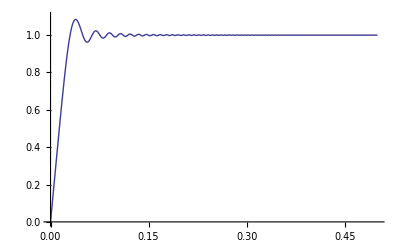

```mathematica
Plot[Sum[coeffslong[[i]]Sqrt[x]*BesselJ[1/4,y1primezeros[[i]]^2*x^2/2],{i,1,600}],{x,0,0.5},PlotRange->{{0,0.5},{0,1.1}}]
```

## Irandoust check

```mathematica
DSolve[y''[x]+(1-x^2)y[x]==0,y[x],x]
```

{{y[x]→ⅇ^(-x^2/2) C[1]+1/2 ⅇ^(-x^2/2) √π C[2] Erfi[x]}}

```mathematica
DSolve[y''[x]+(m^2-x^2)y[x]==0,y[x],x]
```

{{y[x]→C[2] ParabolicCylinderD[1/2 (-1-m^2),ⅈ √2 x]+C[1] ParabolicCylinderD[1/2 (-1+m^2),√2 x]}}

```mathematica
Limit[ParabolicCylinderD[1/2 (-1-m^2),ⅈ √2 x],x->0]
```

(2^(-1/4-m^2/4) √π)/Gamma[1/4 (3+m^2)]

```mathematica
Limit[ParabolicCylinderD[1/2 (-1+m^2),√2 x],x->0]
```

(2^(1/4 (-1+m^2)) √π)/Gamma[3/4-m^2/4]

```mathematica
Limit[ParabolicCylinderD[1/2 (-1-m^2),ⅈ √2 x],x->0]
```

(2^(-1/4-m^2/4) √π)/Gamma[1/4 (3+m^2)]

```mathematica
FunctionExpand[ParabolicCylinderD[1/2 (-1+m^2),√2 x]]
```

2^(1/4 (1-m^2)) ⅇ^(-x^2/2) HermiteH[1/2 (-1+m^2),x]

```mathematica
FunctionExpand[ⅇ^(-x^2/2)Erfi[x]]
```

ⅇ^(-x^2/2) Erfi[x]

```mathematica
DSolve[y''[x]+(1-x^2)m^2 y[x]==0,y[x],x]
```

{{y[x]→C[2] ParabolicCylinderD[1/2 (-1-m),ⅈ √2 √m x]+C[1] ParabolicCylinderD[1/2 (-1+m),√2 √m x]}}

```mathematica
Limit[ParabolicCylinderD[1/2 (-1-m),ⅈ √2 √m x],x->0]
```

(2^(-1/4-m/4) √π)/Gamma[(3+m)/4]

```mathematica
Limit[ParabolicCylinderD[1/2 (-1+m),√2 √m x],x->0]
```

(2^(1/4 (-1+m)) √π)/Gamma[3/4-m/4]

```mathematica
Limit[HermiteH[1/2 (-1+m^2),x],x->0]
```

(2^(1/2 (-1+m^2)) √π)/Gamma[3/4-m^2/4]

```mathematica
Limit[Erfi[x],x->0]
```

0

```mathematica
sol=ⅇ^(-x^2/2)  Erfi[x]
```

ⅇ^(-x^2/2) Erfi[x]

```mathematica
FullSimplify[D[sol,{x,2}]+sol*(1-x^2)]
```

0

```mathematica
solm=ⅇ^(-(m^4 x^2)/2) Erfi[m^2 x]
```

ⅇ^(-1/2 m^4 x^2) Erfi[m^2 x]

```mathematica
FullSimplify[D[solm,{x,2}]+solm*(m^2-x^2)]
```

ⅇ^(-1/2 m^4 x^2) (m^2-m^4-x^2+m^8 x^2) Erfi[m^2 x]

```mathematica
FullSimplify[D[sol,{x,2}]]
```

ⅇ^(-x^2/2) (-1+x^2) Erfi[x]

```mathematica
soltry=Exp[-m^2 x^2/2]Erfi[m x]
```

ⅇ^(-1/2 m^2 x^2) Erfi[m x]

```mathematica
D[soltry,{x,2}]
```

(-ⅇ^(-1/2 m^2 x^2) m^2+ⅇ^(-1/2 m^2 x^2) m^4 x^2) Erfi[m x]

```mathematica
solerfc=ⅇ^(-x^2/2)  Erfc[x]
```

ⅇ^(-x^2/2) Erfc[x]

```mathematica
FullSimplify[D[solerfc,{x,2}]]
```

ⅇ^(-(3 x^2)/2) ((8 x)/(√π)+ⅇ^(x^2) (-1+x^2) Erfc[x])

```mathematica
real1= ParabolicCylinderD[1/2 (-1-m),ⅈ √2 √m x]
```

ParabolicCylinderD[1/2 (-1-m),ⅈ √2 √m x]

```mathematica
real2=ParabolicCylinderD[1/2 (-1+m),√2 √m x]
```

ParabolicCylinderD[1/2 (-1+m),√2 √m x]

```mathematica
Limit[real1,x->0]
```

(2^(-1/4-m/4) √π)/Gamma[(3+m)/4]

```mathematica
Limit[real2,x->0]
```

(2^(1/4 (-1+m)) √π)/Gamma[3/4-m/4]

```mathematica
FunctionExpand[ParabolicCylinderD[1/2 (-1-m),ⅈ √2 √m x]]
```

2^((1+m)/4) ⅇ^((m x^2)/2) HermiteH[1/2 (-1-m),ⅈ √m x]

```mathematica
FunctionExpand[ParabolicCylinderD[1/2 (-1+m),√2 √m x]]
```

2^((1-m)/4) ⅇ^(-(m x^2)/2) HermiteH[1/2 (-1+m),√m x]

```mathematica
h=Exp[-1/2*m*x^2]phi[x]
```

ⅇ^(-(m x^2)/2) phi[x]

```mathematica
FullSimplify[D[h,{x,2}]+m^2(1-x^2)h]
```

ⅇ^(-(m x^2)/2) ((-1+m) m phi[x]-2 m x phi'[x]+phi''[x])

```mathematica
Clear[y]
```

```mathematica
DSolve[{a''[x]-2m x a'[x]+a[x]*m(m-1)==0,a'[1]==0,a[0]==0},a[x],x]
```

{{a[x]→0}}

```mathematica
Limit[ Hypergeometric1F1[(1-m)/4,1/2,m x^2],x->0]
```

1

```mathematica
Limit[HermiteH[1/2 (-1+m),√m x],x->0]
```

(2^(1/2 (-1+m)) √π)/Gamma[3/4-m/4]

```mathematica
coeffs={1.0,0.33333333333333331,0.10000000000000001,0.023809523809523808,0.0046296296296296294,0.00075757575757575758,0.00010683760683760684,1.3227513227513228*^-05,1.4589169000933706*^-06,1.4503852223150468*^-07,1.3122532963802804*^-08,1.0892221037148573*^-09,8.3507027951472384*^-11,5.9477940136376346*^-12,3.9554295164585257*^-13,2.4668270102644567*^-14,1.4483264643598136*^-15,8.032735012415772*^-17,4.2214072888070875*^-18,2.1078551914421354*^-19,1.0025164934907718*^-20,4.5518467589281999*^-22,1.9770647538779051*^-23,8.2301492992142201*^-25,3.2892603491757513*^-26,1.2641078988989162*^-27,4.678483515518485*^-29,1.6697617934173718*^-30,5.7541916439821706*^-32,1.9169428621097819*^-33,6.180307588222794*^-35}
```

{1.,0.333333,0.1,0.0238095,0.00462963,0.000757576,0.000106838,0.0000132275,1.45892×10^-6,1.45039×10^-7,1.31225×10^-8,1.08922×10^-9,8.3507×10^-11,5.94779×10^-12,3.95543×10^-13,2.46683×10^-14,1.44833×10^-15,8.03274×10^-17,4.22141×10^-18,2.10786×10^-19,1.00252×10^-20,4.55185×10^-22,1.97706×10^-23,8.23015×10^-25,3.28926×10^-26,1.26411×10^-27,4.67848×10^-29,1.66976×10^-30,5.75419×10^-32,1.91694×10^-33,6.18031×10^-35}

```mathematica
y[x_]:=Sum[coeffs[[i]]*x^(2*(i-1)+1),{i,1,30}]
```

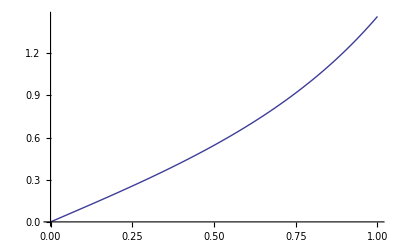

```mathematica
Plot[y[x],{x,0,1}]
```

```mathematica
For[i=1;temp=1;tab=List[1],i<30,i++,temp=temp*(4*m*(i-1)+3*m-m^2)/((2*(i-1)+3)*(2(i-1)+2));Print[temp];tab=Append[tab,temp]]
```

1/6 (3 m-m^2)

1/120 (3 m-m^2) (7 m-m^2)

((3 m-m^2) (7 m-m^2) (11 m-m^2))/5040

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2))/362880

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2))/39916800

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2))/6227020800

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2))/1307674368000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2))/355687428096000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2))/121645100408832000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2))/51090942171709440000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2))/25852016738884976640000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2))/15511210043330985984000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2))/10888869450418352160768000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2))/8841761993739701954543616000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2))/8222838654177922817725562880000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2))/8683317618811886495518194401280000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2))/10333147966386144929666651337523200000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2))/13763753091226345046315979581580902400000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2))/20397882081197443358640281739902897356800000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2))/33452526613163807108170062053440751665152000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2))/60415263063373835637355132068513997507264512000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2))/119622220865480194561963161495657715064383733760000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2))/258623241511168180642964355153611979969197632389120000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2) (95 m-m^2))/608281864034267560872252163321295376887552831379210240000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2) (95 m-m^2) (99 m-m^2))/1551118753287382280224243016469303211063259720016986112000000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2) (95 m-m^2) (99 m-m^2) (103 m-m^2))/4274883284060025564298013753389399649690343788366813724672000000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2) (95 m-m^2) (99 m-m^2) (103 m-m^2) (107 m-m^2))/12696403353658275925965100847566516959580321051449436762275840000000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2) (95 m-m^2) (99 m-m^2) (103 m-m^2) (107 m-m^2) (111 m-m^2))/40526919504877216755680601905432322134980384796226602145184481280000000000000

((3 m-m^2) (7 m-m^2) (11 m-m^2) (15 m-m^2) (19 m-m^2) (23 m-m^2) (27 m-m^2) (31 m-m^2) (35 m-m^2) (39 m-m^2) (43 m-m^2) (47 m-m^2) (51 m-m^2) (55 m-m^2) (59 m-m^2) (63 m-m^2) (67 m-m^2) (71 m-m^2) (75 m-m^2) (79 m-m^2) (83 m-m^2) (87 m-m^2) (91 m-m^2) (95 m-m^2) (99 m-m^2) (103 m-m^2) (107 m-m^2) (111 m-m^2) (115 m-m^2))/138683118545689835737939019720389406345902876772687432540821294940160000000000000

```mathematica
solseries[x_]:=Sum[tab[[i]]*x^(2*(i-1)+1),{i,1,30}]
```

```mathematica
Plot[solseries[x]/.{m->1},{x,0,1}]
```

-Graphics-

```mathematica
solseriesder[x_]:=Sum[tab[[i]]*(2*(i-1)+1)*x^(2*(i-1)),{i,1,30}]
```

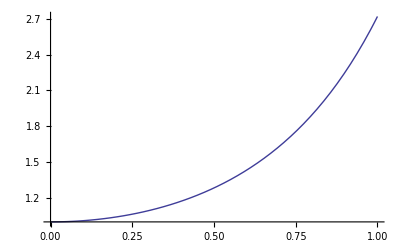

```mathematica
Plot[solseriesder[x]/.{m->1},{x,0,1}]
```

```mathematica
Table[FindRoot[solseriesder[1]-solseries[1]*m,{m,30+i/10}],{i,1,100}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot will be suppressed during this calculation.

{{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→30.2727},{m→26.3048},{m→26.3048},{m→22.3152},{m→18.3157},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→34.2074},{m→30.2727},{m→30.2727},{m→26.3048},{m→22.3152},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025},{m→38.1025}}

```mathematica
eig={2.2631105380370293,6.29768520284807,10.307726795402782,14.312786408192768,18.31566692902573,22.31523617697906,26.30480463074491,30.27270817974602,34.20742244520866,38.10248626414265}
```

{2.26311,6.29769,10.3077,14.3128,18.3157,22.3152,26.3048,30.2727,34.2074,38.1025}

```mathematica
one=Table[NIntegrate[(1-x^2)*(Exp[-eig[[i]]/2*x^2](solseries[x]/.{m->eig[[i]]})),{x,0,1}],{i,1,10}]
```

{0.195249,0.0252138,0.00941183,0.0048815,0.00298056,0.00201093,0.00143497,0.001116,0.000808425,0.000761123}

```mathematica
second=Table[NIntegrate[(1-x^2)*(Exp[-eig[[i]]*x^2](solseries[x]/.{m->eig[[i]]})^2),{x,0,1}],{i,1,10}]
```

{0.072411,0.00980517,0.00368137,0.0019128,0.00116899,0.000787772,0.000566885,0.000427713,0.000334433,0.000268805}

```mathematica
mix=NIntegrate[(1-x^2)*Exp[-(eig[[4]]+eig[[6]])/2*x^2](solseries[x]/.{m->eig[[4]]})*(solseries[x]/.{m->eig[[6]]}),{x,0,1}]
```

-4.99062×10^-7

```mathematica
am=Table[one[[i]]/second[[i]],{i,1,10}]
```

{2.6964,2.57148,2.55661,2.55202,2.54969,2.55268,2.53132,2.60922,2.4173,2.8315}

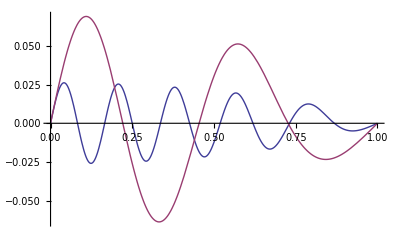

```mathematica
Plot[{((1-x^2)solseries[x]*Exp[-1/2*m*x^2])/.{m->eig[[10]]},((1-x^2)solseries[x]*Exp[-1/2*m*x^2])/.{m->eig[[4]]}},{x,0,1}]
```

```mathematica
given={1.3382,-0.5455,0.3589,-0.2721,0.2211,-0.1873,0.1631,-0.1339,0.1306,-0.1191}
```

{1.3382,-0.5455,0.3589,-0.2721,0.2211,-0.1873,0.1631,-0.1339,0.1306,-0.1191}

```mathematica
overall[x_]:=Sum[am[[i]]*(solseries[x]*Exp[-1/2*m*x^2])/.{m->eig[[i]]},{i,1,10}]
```

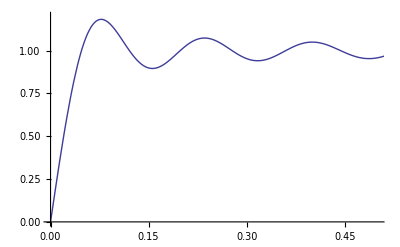

```mathematica
Plot[overall[x],{x,0,1},PlotRange->{{0,0.5},{0,1.2}}]
```

```mathematica
NMaximize[{D[(solseries[x]*Exp[-eig[[1]]*x^2/2])/.{m->eig[[1]]},{x,2}]+eig[[1]]^2(1-x^2)*(solseries[x]*Exp[-eig[[1]]*x^2/2])/.{m->eig[[1]]},x≥ 0,x≤1},x]
```

{4.44089×10^-15,{x→0.972872}}

```mathematica
Limit[Sqrt[x]BesselY[1/4,m^2 x^2/2],x->0]
```

-(√2 (m^2)^(3/4) Gamma[1/4])/(m^2 π)